# Data Analysis in Astronomy and Physics

## Lecture 5: Probability Distributions

M. Röllig

## Introduction

A probability distribution 𝒻(x) describes the expectation of occurrence of event x.

Example: Toss 4 coins simultaneously. 
The probability of 	no heads is		 (1/2)^4=1/16
				1 head 			4×(1/2)^4=4/16
				two heads 		6×(1/2)^4=6/16   (  (4
2)=6 )
				three heads 		4×(1/2)^4=4/16
				and four heads	(1/2)^4=1/16. 
				
				The probability sum of all possibilities is 1.
				
If x is the number of heads x={0,1,2,3,4}, 
the corresponding  probabilities are 𝒫(x)=(1/16, 4/16, 6/16, 4/16,1/16}, a distribution of probabilities describing our expectation of the outcome of the experiment.

## Introduction

In the example we have a mapping between a set of integer numbers and the outcome of the experiment.

If the outcome does not correspond to discrete numbers, we have a mapping of a set of outcomes to real numbers. If so, we discretize the real numbers into small sub-ranges, in which we assume that the probability does not change.

The real number x indexing an outcome is associated with a probability density 𝒻(x), such that the probability of getting a number near x, say in the range δx, is 𝒫(x)δx.

## Definition

If x is a continuous random variable, then 𝒻(x) is its probability density function (PDF), commonly called probability distribution, when,

𝒫(a<x<b)=∫_a^b 𝒻(x)ⅆx

∫_(-∞)^∞ 𝒻(x)ⅆx=1, and

𝒻(x) is a single-valued non-negative number for all real x.

## Definition

The corresponding cumulative probability distribution function (CDF) is ℱ(x)=∫_(-∞)^x 𝒻(y)ⅆy.

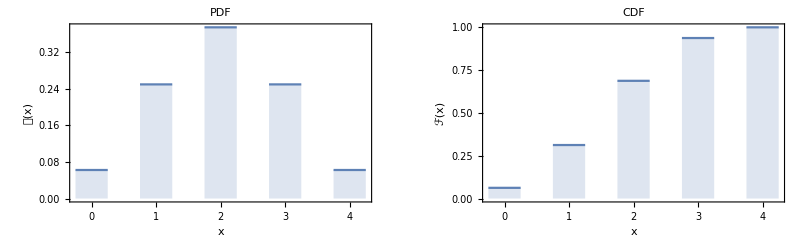

```mathematica
With[{d=EmpiricalDistribution[{1/16, 4/16, 6/16, 4/16,1/16}->{0,1,2,3,4}]},GraphicsRow[{DiscretePlot[PDF[d,x],{x,0,4},ExtentSize->.5,Frame->True,FrameLabel->{x,𝒻[x]},BaseStyle->{FontSize->14,FontFamily->"Times"},PlotLabel->"PDF"],
DiscretePlot[CDF[d,x],{x,0,4},ExtentSize->.5,Frame->True,FrameLabel->{x,ℱ[x]},BaseStyle->{FontSize->14,FontFamily->"Times"},PlotLabel->"CDF"]},ImageSize->Full]]
```

If distributions are functions of more than one variable they are called multivariate.

## Distribution Measures

To quantify a distribution, one can describe its location (“Where is the center?”) and its dispersion (“What is its spread/width?”).

These quantifiers can be given by the first two moments of the distributions:

mean:		μ_1=μ=∫_(-∞)^∞ x 𝒻(x)ⅆx

			variance:		μ_2=σ^2=∫_(-∞)^∞ (x-μ_1)^2 𝒻(x)ⅆx

The square root of the variance is called standard deviation σ.

Higher moments exist as well (third moment ~ “skewness”). There are probability distributions we can calculate resulting from ideal experiments, outcomes or combinations of these. The best-known are the UNIFORM, BINOMIAL, POISSON and GAUSSIAN (or NORMAL) distributions.

### Expectation values

Parameters such as  μ and σ of the Poisson or Gaussian distribution define these distribution functions. They are not statistics! (Statistics are a function of data!). But we may expect or anticipate that our data follows a certain distribution and we may wish to relate statistics from the data to parameters describing the distribution.

This is done through expectation values. The expectation E[ℊ(x)] of some function ℊ(x) of a random variable x, with distribution function 𝒻(x), is defined as

```mathematica
equation["E"[ℊ[x]]==∫ℊ[x]𝒻[x]ⅆx]
```

E(ℊ(x))==∫ℊ(x) 𝒻(x)ⅆx

i.e. the sum of all possible values of 𝒻 weighted by the probability of their occurrence. Think of the expectation as being the result of repeating an experiment many times, and averaging the results.

### Expectation values

For example, compute an average value of ⟨X⟩. If we repeat the experiment many times, we will find that the average of ⟨X⟩ will converge to the true mean value, the expectation of the function 𝒻(x)=x.

```mathematica
equation["E"[x]==∫x 𝒻[x]ⅆx]
```

E(x)==∫x 𝒻(x)ⅆx

Likewise, the statistics S^2 should converge to the variance defined by

```mathematica
equation[var[(x-μ)^2]=="E"[(x-μ)^2]==∫(x-μ)^2 𝒻[x]ⅆx]
```

var((x-μ)^2)==E((x-μ)^2)==∫(x-μ)^2 𝒻(x)ⅆx

In fact (⟨X⟩,S^2) (functions of data alone) converge to (μ, σ^2) when we have plenty of data.

#### Convention

We will in the following use the convention that if applicable, Greek letters describe the whole population while Latin letters describe sample statistics, e.g. a population might be normally distributed with mean μ and variance σ^2, while a sample from this sample will be distributed around the sample mean x̄ and the sample variance S^2.

## Moments of a distribution

Expectations of a distribution can also be expressed in terms of moments. For the list {x_1,x_2,…,x_n}, the r^th central moment is given by 1/n∑_i (x_i-x̄)^r, where x̄ is the mean of the list.

```mathematica
equation[Subscript[μ, r]==∫(x-μ)^r 𝒻[x]ⅆx]
```

μ_r==∫(x-μ)^r 𝒻(x)ⅆx

## Moments of a distribution

The zero-th moment is just the area of 𝒻(x).

```mathematica
equation[Subscript[μ, 0]==∫𝒻[x]ⅆx]
```

μ_0==∫𝒻(x)ⅆx

The second moment is the variance:

```mathematica
equation[Subscript[μ, 2]==σ^2==∫(x-μ)^2 𝒻[x]ⅆx]
```

μ_2==σ^2==∫(x-μ)^2 𝒻(x)ⅆx

## Moments of a distribution

The skewness is

```mathematica
equation[Subscript[γ, 1]=Subscript[μ, 3]/Subscript[μ, 2]^(3/2)==(∫(x-μ)^3 𝒻[x]ⅆx)/((∫(x-μ)^2 𝒻[x]ⅆx)^(3/2))]
```

γ_1=μ_3/μ_2^(3/2)==(∫(x-μ)^3 𝒻(x)ⅆx)/((∫(x-μ)^2 𝒻(x)ⅆx)^(3/2))

Skewness measures the asymmetry of a distribution/data. A positive skewness indicates a distribution with a long right tail, a negative skewness a distribution with a long left tail.

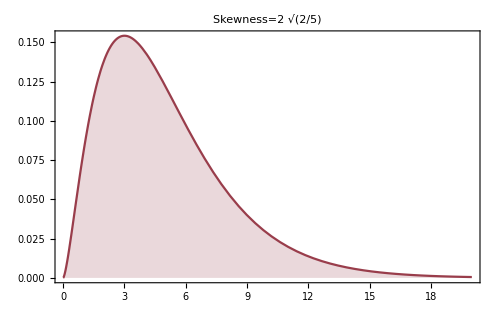
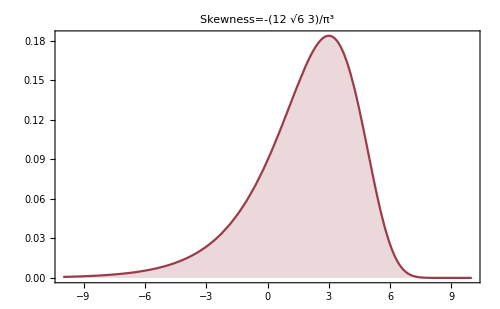

```mathematica
Row[{Plot[PDF[ChiSquareDistribution[5],x],{x,0,20},Filling->Axis,BaseStyle->{FontSize->16,FontFamily->"Times"},PlotLabel->Row[{"Skewness=",Skewness[ChiSquareDistribution[5]]}]],
Spacer[40],
Plot[PDF[GumbelDistribution[3,2],x],{x,-10,10},Filling->Axis,
BaseStyle->{FontSize->16,FontFamily->"Times"},PlotLabel->Row[{"Skewness=",Skewness[GumbelDistribution[3,2]]}]]}]
```

## Moments of a distribution

ATTENTION: Abramowitz and Stegun (1972, p. 928) also confusingly refer to both γ_1 and β=γ_1^2 as "skewness."

Several types of skewness are defined, the terminology and notation of which are unfortunately rather confusing.

For a summary see :http://mathworld.wolfram.com/Skewness.html

## Moments of a distribution

Kurtosis is defined as a normalized form of the fourth central moment μ_4 of a distribution and is a measure of the degree of peakiness(e.g.: 3 for Gaussian):

```mathematica
equation[Subscript[β, 2]=Subscript[μ, 4]/Subscript[μ, 2]^2==(∫(x-μ)^4 𝒻[x]ⅆx)/((∫(x-μ)^2 𝒻[x]ⅆx)^2)]
```

β_2=μ_4/μ_2^2==(∫(x-μ)^4 𝒻(x)ⅆx)/((∫(x-μ)^2 𝒻(x)ⅆx)^2)

```mathematica
Integrate[(x-0)^4 PDF[NormalDistribution[0,2],x],{x,-∞,+∞}]/(Integrate[(x-0)^2 PDF[NormalDistribution[0,2],x],{x,-∞,+∞}]^2)
```

3

### Moments of spectra

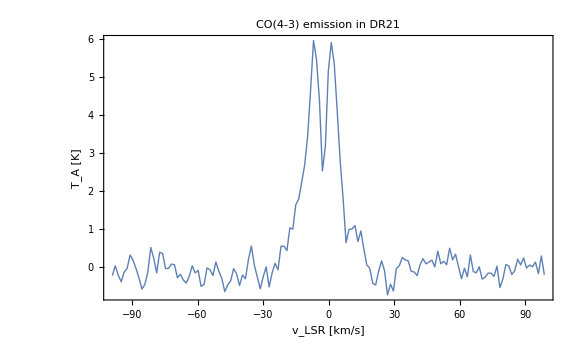

```mathematica
spectrum=Cases[Most@Import["http://hera.ph1.uni-koeln.de/ftpspace/roellig/Data%20Analysis/co_4-3_80.dat","Table","HeaderLines"->0],{a_,b_}/;Abs[a]<100.];
ListPlot[spectrum,Joined->True,FrameLabel->{"v_LSR [km/s]","T_A [K]"},PlotLabel->"CO(4-3) emission in DR21"(*,PlotRange->{{-100,100},{-2,12}}*),BaseStyle->{FontSize->21},ImageSize->Large,PlotRange->All,Frame->True,Axes->False,PlotStyle->Thick]
```

```mathematica
spectrum[[100;;102]]
```

{{35.0739,0.171445},{36.429,0.150318},{37.784,-0.127574}}

Imagine we want to characterize the observed spectral emission line. Interesting statistics on are, e.g. the peak position, the integrated line intensity,

### Moments of spectra

The  line integrated intensity is given by the 0^th moment, ∫I(V)ⅆv, or in case of the discrete data points: Δv∑_i I_i (if the velocity channels are equally wide).

```mathematica
equation[Subscript[M, 0]==Δv∑_i Subscript["I", i]]
```

M_0==Δv ∑_i I_i

The first moment defines the intensity-weighted velocity of the spectral line. It can be taken as a measure for the mean velocity of the gas. The first moment is defined by

```mathematica
equation[Subscript[M, 1]==(∑_i Subscript[v, i] Subscript["I", i])/(∑_i Subscript["I", i])]
```

M_1==(∑_i v_i I_i)/(∑_i I_i)

### Moments of spectra

The second moment is a measure for the velocity dispersion, σ, of the gas along the line of  sight, i.e. the width of the spectral line. It is defined by the intensity-weighted square of the velocity:

```mathematica
equation[Subscript[M, 2]==√((∑_i (Subscript[v, i]-Subscript[M, 1])^2 Subscript["I", i])/(∑_i Subscript["I", i]))]
```

M_2==√((∑_i (v_i-M_1)^2 I_i)/(∑_i I_i))

### Moments of spectra

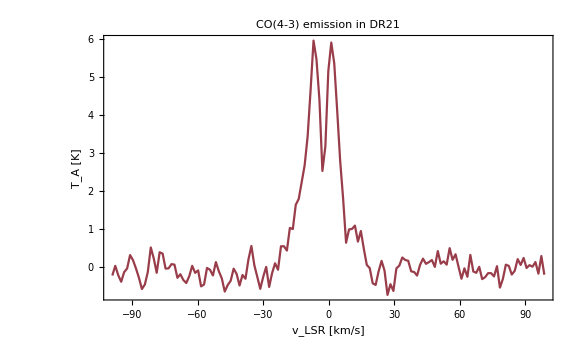

```mathematica
spectrum=Cases[Most@Import["http://hera.ph1.uni-koeln.de/ftpspace/roellig/Data%20Analysis/co_4-3_80.dat","Table","HeaderLines"->0],{a_,b_}/;Abs[a]<100.];
ListPlot[spectrum,Joined->True,FrameLabel->{"v_LSR [km/s]","T_A [K]"},PlotLabel->"CO(4-3) emission in DR21"(*,PlotRange->{{-100,100},{-2,12}}*),BaseStyle->{FontSize->21},ImageSize->Large]
```

```mathematica
deltaV=Mean@Differences@spectrum[[All,1]]
M0=deltaV*Total[spectrum[[All,2]]]
```

1.35505

82.1292

### Moments of spectra

Assuming a proper baseline, the integrate line intensity is 82 K km/s

Where is the center (of mass) of the spectrum? (∫_(-∞)^∞ v Iⅆv)/(∫_(-∞)^∞ Iⅆv)==⟨v⟩

```mathematica
M1=Total[spectrum[[All,1]]spectrum[[All,2]]]/Total[spectrum[[All,2]]]
```

1.59657

And what is the FWHM (full width half maximum):

```mathematica
M2=√Abs@(Total[(spectrum[[All,1]]-M1)^2 spectrum[[All,2]]]/Total[spectrum[[All,2]]])
```

23.1812

## Overview table

```mathematica
tab={{
"Uniform","𝒻(x;a,b)=",PDF[UniformDistribution[{a,b}],x]//TraditionalForm,Mean[UniformDistribution[{a,b}]],Variance[UniformDistribution[{a,b}]],"In the study of rounding errors; as a tool in studies of other continuous distributions"},
{"Binomial","𝒻(x;n,p)=",TraditionalForm[PDF[BinomialDistribution[n,p],x]],Mean[BinomialDistribution[n,p]],Variance[BinomialDistribution[n,p]],"x is the number of successes in an experiment (with n trials) with two possible outcomes, one (\"success\") of probability p, and the other (\"failure\") with probability Cell["q=1-p",ExpressionUUID->"5edfee78-68c9-4e2a-9a92-1e9bcbfac2e8"]. Becomes a Normal distribution when Cell["n → ∞",ExpressionUUID->"7d467820-09cb-4aae-b38a-e03ae1316e1d"]."},
{"Poisson","𝒻(x;μ)=",TraditionalForm[PDF[PoissonDistribution[μ],x]],Mean[PoissonDistribution[μ]],Variance[PoissonDistribution[μ]],"The limit for the Binomial distribution as p≪1, setting Cell["μ=n p",ExpressionUUID->"3529a7f8-93cb-43cc-bc07-c171cfc906ac"]. It is the count-rate distribution, e.g. take a star from which an average of μ photons are received per hour (out of a total of n emitted; hence p≪1); the probability of receiving xphotons in Δt is 𝒻(x;μ). Tends to the Normal distribution as  Cell["μ → ∞",ExpressionUUID->"99364511-3fa4-4ada-9782-59981bed4d47"]."},
{"Normal\n(Gaussian)","𝒻(x;μ,σ)=",TraditionalForm[PDF[NormalDistribution[μ,σ],x]],Mean[NormalDistribution[μ,σ]],Variance[NormalDistribution[μ,σ]],"The essential distribution; The central limit theorem ensures that the majority of \"scattering things\" are dispersed according to Cell["𝒻(x;μ,σ)",ExpressionUUID->"b043f1c2-b8f5-454b-82da-e4871fd8432a"]."},
{"Chi-square","𝒻(χ^2;ν)=",TraditionalForm[PDF[ChiSquareDistribution[ν],x]],Mean[ChiSquareDistribution[ν]],Variance[ChiSquareDistribution[ν]],"Vital in the comparison of samples, model testing; characterizes the dispersion of observed samples from the expected dispersion because if x_i is a sample of Cell["ν",ExpressionUUID->"ee09476c-3a1a-49de-94fc-661ae2cd3eb0"] variables normally and independently distributed with means μ_i and variances σ_i^2, then χ^2=∑_(i=1)^N (x_i-μ_i)^2/σ_i obeys 𝒻(χ^2,ν). Invariably tabulated and used in integral form. Tends to Normal distribution as Cell["ν → ∞",ExpressionUUID->"dd194a25-c153-47c5-883c-393302633abe"]."},
{"Student t","𝒻(t;ν)=",TraditionalForm[PDF[StudentTDistribution[ν],x]],Mean[StudentTDistribution[ν]],Variance[StudentTDistribution[ν]],"For comparison of means, Normally distributed populations; if n x_i's are taken from a Normal population Cell["(μ,σ)",ExpressionUUID->"80238ec2-8759-4803-a9a4-cbb0d267acb9"], and if x_s and σ_s are determined, then t=√(n(OverBar[x_s]-μ))/σ_s, is distributed as 𝒻(t,ν) where \"degrees of freedom\" ν=n-1. Statistic Cell["t",ExpressionUUID->"a7bcd8ad-c9e5-4c2f-9d14-fc0ef5854365"] can also be formulated to compare means for samples from Normal populations with the same σ, different μ. Tends to Normal as Cell["ν → ∞",ExpressionUUID->"e5aacd9e-2739-4678-bb27-6cc6dec19b6c"]."}};
Panel@Grid[tab,Alignment->Left,BaseStyle->{FontFamily->"Times",FontSize->19},Frame->All]
```

Uniform | 𝒻(x;a,b)= | Piecewise[{{1/(b-a), a≤x≤b}, {0, True}}] | (a+b)/2 | 1/12 (-a+b)^2 | In the study of rounding errors; as a tool in studies of other continuous distributions
Binomial | 𝒻(x;n,p)= | Piecewise[{{p^x Binomial[n, x] (1-p)^(n-x), 0≤x≤n}, {0, True}}] | n p | n (1-p) p | x is the number of successes in an experiment (with n trials) with two possible outcomes, one ("success") of probability p, and the other ("failure") with probability Cell["q=1-p"]. Becomes a Normal distribution when Cell["n → ∞"].
Poisson | 𝒻(x;μ)= | Piecewise[{{(ⅇ^-μ μ^x)/(x!), x≥0}, {0, True}}] | μ | μ | The limit for the Binomial distribution as p≪1, setting Cell["μ=n p"]. It is the count-rate distribution, e.g. take a star from which an average of μ photons are received per hour (out of a total of n emitted; hence p≪1); the probability of receiving xphotons in Δt is 𝒻(x;μ). Tends to the Normal distribution as  Cell["μ → ∞"].
Normal
(Gaussian) | 𝒻(x;μ,σ)= | (ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ) | μ | σ^2 | The essential distribution; The central limit theorem ensures that the majority of "scattering things" are dispersed according to Cell["𝒻(x;μ,σ)"].
Chi-square | 𝒻(χ^2;ν)= | Piecewise[{{(2^(-ν/2) ⅇ^(-x/2) x^(ν/2-1))/(ν/2), x>0}, {0, True}}] | ν | 2 ν | Vital in the comparison of samples, model testing; characterizes the dispersion of observed samples from the expected dispersion because if x_i is a sample of Cell["ν"] variables normally and independently distributed with means μ_i and variances σ_i^2, then χ^2=∑_(i=1)^N (x_i-μ_i)^2/σ_i obeys 𝒻(χ^2,ν). Invariably tabulated and used in integral form. Tends to Normal distribution as Cell["ν → ∞"].
Student t | 𝒻(t;ν)= | ((ν/(ν+x^2))^((ν+1)/2))/(√ν ν/21/2) | Piecewise[{{0, ν>1}, {Indeterminate, True}}] | Piecewise[{{ν/(-2+ν), ν>2}, {Indeterminate, True}}] | For comparison of means, Normally distributed populations; if n x_i's are taken from a Normal population Cell["(μ,σ)"], and if x_s and σ_s are determined, then t=√(n(OverBar[x_s]-μ))/σ_s, is distributed as 𝒻(t,ν) where \"degrees of freedom\" ν=n-1. Statistic Cell["t"] can also be formulated to compare means for samples from Normal populations with the same σ, different μ. Tends to Normal as Cell["ν → ∞"].

## Binomial Distribution

There are two outcomes - `success’ or `failure’. This common distribution gives the chance of n successes in N trials, with the probability of a success at each trial ρ, and successive trials are independent. This  probability is

```mathematica
equation[𝒻[n,"N",ρ]==Binomial["N",n] ρ^n(1-ρ)^("N"-n)]
```

𝒻(n,N,ρ)==Binomial[N, n] ρ^n (1-ρ)^(N-n)

The first term is the Binomial coefficient (or combinatorial coefficient) and gives the number of distinctive ways of choosing n items out of N.

```mathematica
equation[Binomial["N",n]==("N"!)/(n!("N"-n)!)]
```

Binomial[N, n]==(N!)/(n! (N-n)!)

## Binomial Distribution

### Motivation

Imagine N=5 people want to sit in only n=3 chairs. How many possible arrangements are there (permutations)?

The first chair (C1) can be occupied by 5 different persons. The second chair (C2) can be occupied by 4 different  people (one is already sitting). On the last chair (C3), three different people can sit. In total we have

5×4×3=60 possible ways to arrange 5 people on 3 chairs

Another way of writing this is

(5×4×3×2×1)/(2×1)=5×4×3=60, or generally   (N!)/((N-n)!)

(N!)/((N-n)!) is the number of permutations, i.e. the number of different ways to choose n items from a set of N, when we care about the order!

## Binomial Distribution

### Motivation

When the order is irrelevant, i.e. we just wish to know which combination of people end up sitting on a chair, we have to divide by the different possible combinations of 3 people sitting on 3 chairs, which is 3!.

To get the number of combinations, when choosing n items from a set of N, we find

			(N!)/(n!(N-n)!) which is written shortly as (N
n)

## Binomial Distribution

### Properties

The Binomial distribution has a mean value given by

∑_(n=0)^N n 𝒻(n)=N×p

and a variance of

∑_(n=0)^N (n-N×p)^2 𝒻(n)=N×p×(1-p)

The Binomial distribution converges to a normal distribution as n→∞:

## Binomial Distribution

### Properties

```mathematica
{μ,σ}={Mean[BinomialDistribution[n,p]],StandardDeviation[BinomialDistribution[n,p]]}
```

{n p,√(n (1-p) p)}

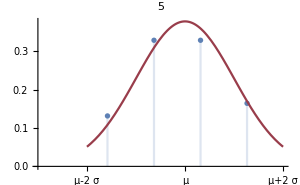
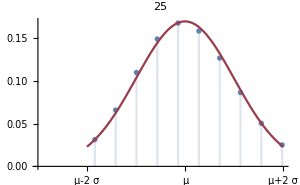
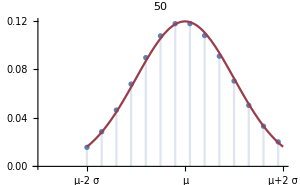
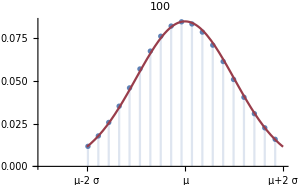

```mathematica
Block[{p=1/3},
Table[Show[DiscretePlot[PDF[BinomialDistribution[n,p],k],{k,Ceiling[μ-2σ],Floor[μ+2σ]},PlotRange->{{μ-3σ,μ+2σ},All},AxesOrigin->{μ-3σ,0}],Plot[PDF[NormalDistribution[μ,σ],x],{x,μ-2σ,μ+2σ}],Ticks->{{{μ-2σ,HoldForm[μ-2σ]},{μ,HoldForm[μ]},{μ+2σ,HoldForm[μ+2σ]}},Automatic},PlotRange->{{μ-3σ,μ+2σ},All},PlotLabel->n,ImageSize->300],{n,{5,25,50,100}}]]
Clear[μ,σ]
```

## Binomial Distribution

### Properties

Skewness measures the asymmetry in a distribution. A positive skewness indicates a distribution with a long right tail. A negative skewness indicates a distribution with a long left tail.

```mathematica
Skewness[BinomialDistribution[n,p]]
```

(1-2 p)/(√(n (1-p) p))

The distribution is symmetric for p=0.5:

```mathematica
Solve[Skewness[BinomialDistribution[n,p]]==0,p]
```

{{p→1/2}}

The distribution becomes symmetric for large n:

```mathematica
Limit[Skewness[BinomialDistribution[n,p]],n->∞]
```

0

## Binomial Distribution

### P.M.F. - probability mass function

𝒻(k; N,ρ)=𝒫(X=n)=(N
n)(ρ^n(1-ρ))^(N-n)

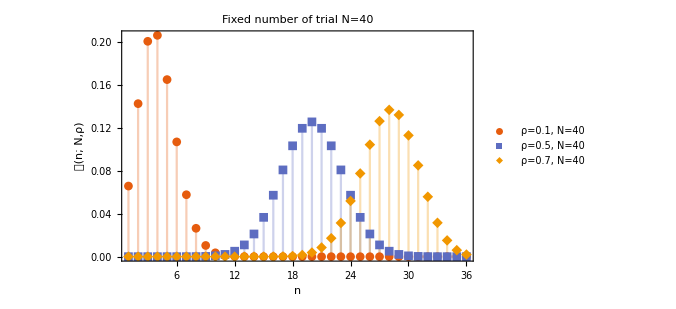
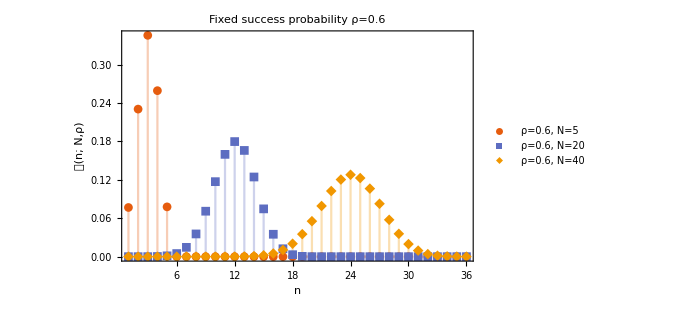
-Graphics- | -Graphics-

```mathematica
Grid[{{DiscretePlot[Evaluate@Table[PDF[BinomialDistribution[40,p],k],{p,{0.1,0.5,0.7}}],{k,36},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,PlotRange->All,PlotMarkers->Automatic,
PlotLabel->"Fixed number of trial N=40",Frame->True,FrameLabel->{"n", "𝒻(n; N,ρ)"},PlotLegends->Placed[{"ρ=0.1, N=40","ρ=0.5, N=40","ρ=0.7, N=40"},Below]],
DiscretePlot[Evaluate@Table[PDF[BinomialDistribution[n,.6],k],{n,{5,20,40}}],{k,36},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,PlotRange->All,PlotMarkers->Automatic,PlotLabel->"Fixed success probability ρ=0.6",
Frame->True,FrameLabel->{"n", "𝒻(n; N,ρ)"},PlotLegends->Placed[{"ρ=0.6, N=5","ρ=0.6, N=20","ρ=0.6, N=40"},Below]]}},Spacings->2]
```

The term probability mass function is used for discrete random variables.

## Binomial Distribution

### Example

According to the latest exoplanet data (numbers made up!), a stellar system has a 56% chance to host at least one planet. What is the probability that in a random sample of 10 stars exactly 6 will host at least one planet?

𝒫(X=6)=(10
6)0.56^6(1-0.56)^(10-6)= 210×0.56^6×0.44^4=0.243

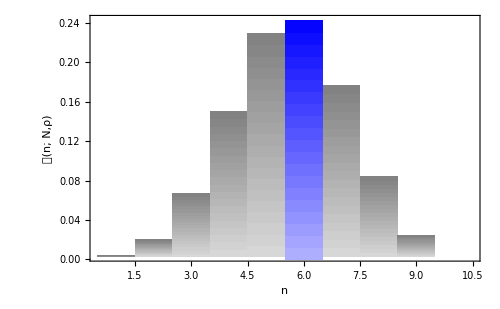

```mathematica
Show[{DiscretePlot[PDF[BinomialDistribution[10,0.56],k],{k,1,10},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,PlotRange->All,Frame->True,FrameLabel->{"n", "𝒻(n; N,ρ)"},ExtentSize->Full,ExtentElementFunction->"FadingRectangle", PlotStyle->Gray],DiscretePlot[PDF[BinomialDistribution[10,0.56],k],{k,6,6},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,PlotRange->All,Frame->True,FrameLabel->{"n", "𝒻(n; N,ρ)"},ExtentSize->Full,ExtentElementFunction->"FadingRectangle",PlotStyle->Blue]}]
```

## Binomial Distribution

Success-failure rule: 

A binomial distribution with at least 10 expected successes and 10 expected failures closely follows a normal distribution.

				n×p≥10
				n×(1-p)≥10

Normal approximation to the binomial: If the success- failure condition holds,

			Binomial(n,p) ≈ Normal(μ,σ)   ,  where μ=n×p,  and σ=√(n×p×(1-p))

## Quiz

What is is the minimum required n for a binomial distribution with p = 0.21 to closely follow a normal distribution?

## Binomial Distribution

### Example

Describe the probability distribution  of stellar systems hosting at least one planet among a random sample of 100.

p=0.56, n=100
expected successes:    	p×n=56  >10    		expected fails:    (1-p)×n=44  >10     

					μ=56					σ=√(100×0.56×0.44)=4.96

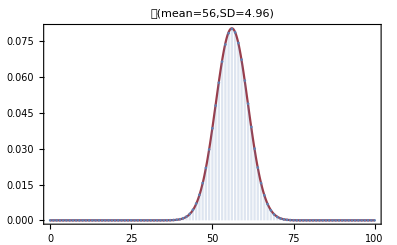

```mathematica
Show[{
Plot[PDF[NormalDistribution[56,4.96],x],{x,0,100},BaseStyle->{16,FontFamily->"Times"},PlotLabel->"𝒩(mean=56,SD=4.96)",ImageSize->Medium],DiscretePlot[PDF[BinomialDistribution[100,0.56],x],{x,0,100}]}]
```

### Example

What is the probability, that at least 60 out of a random sample of 100 stellar systems host a planet?

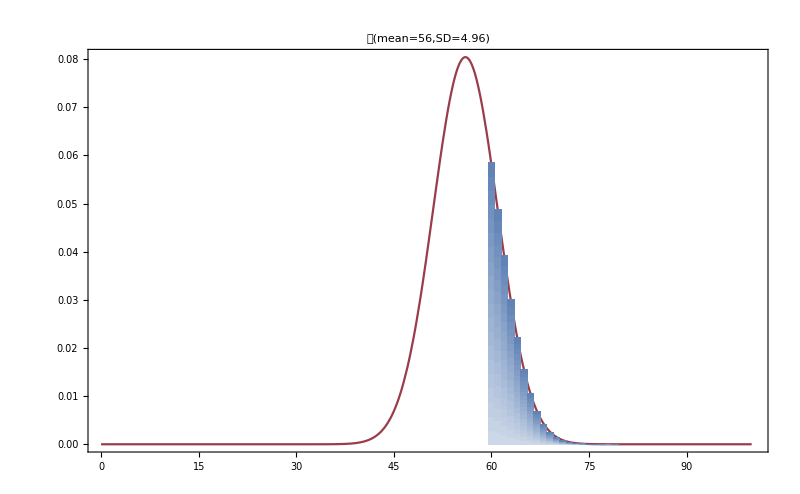

```mathematica
Show[{Plot[PDF[NormalDistribution[56,4.96],x],{x,0,100},BaseStyle->{16,FontFamily->"Times"},PlotLabel->"𝒩(mean=56,SD=4.96)",ImageSize->Medium],DiscretePlot[PDF[BinomialDistribution[100,0.56],x],{x,60,100},ExtentSize->Full,ExtentElementFunction->"FadingRectangle"]},ImageSize->800]
```

### Example

What is the probability, that at least 60 out of a random sample of 100 stellar systems host a planet?

```mathematica
Total[Table[PDF[BinomialDistribution[100,0.56],x],{x,60,100}]]
```

0.241106

Using the normal distribution as approximation for the Binomial distribution gives 
slightly different result!

```mathematica
1-CDF[NormalDistribution[56,4.96],60]
```

0.209991

We have to account for the discreteness of the Binomial distribution.

```mathematica
1-CDF[NormalDistribution[56,4.96],59.5]
```

0.240204

## Binomial Distribution

### CDF - cumulative distribution function

ℱ(k; N,ρ)=𝒫(X≤k)=∑_(n=0)^k (N
n)(ρ^n(1-ρ))^(N-n)

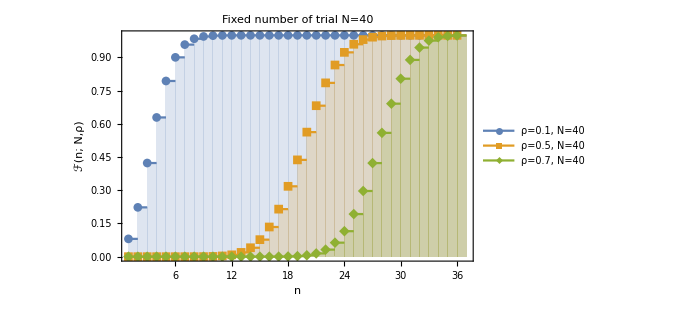
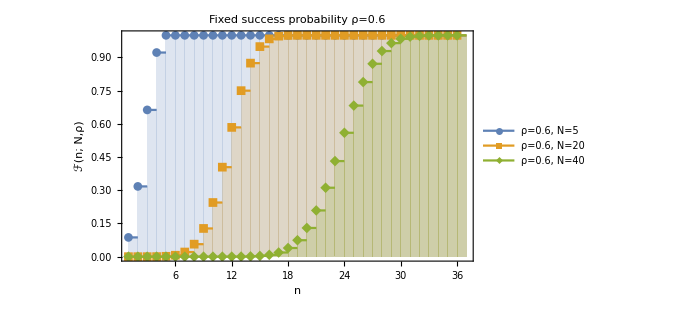
-Graphics- | -Graphics-

```mathematica
Grid[{{DiscretePlot[Evaluate@Table[CDF[BinomialDistribution[40,p],k],{p,{0.1,0.5,0.7}}],{k,36},ExtentSize->Right,PlotRange->All,PlotMarkers->Automatic,Frame->True,BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,FrameLabel->{"n", "ℱ(n; N,ρ)"},PlotLabel->"Fixed number of trial N=40",PlotLegends->Placed[{"ρ=0.1, N=40","ρ=0.5, N=40","ρ=0.7, N=40"},Below]],DiscretePlot[Evaluate@Table[CDF[BinomialDistribution[n,.6],k],{n,{5,20,40}}],{k,36},ExtentSize->Right,PlotRange->All,PlotMarkers->Automatic,Frame->True,BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,PlotLabel->"Fixed success probability ρ=0.6",FrameLabel->{"n", "ℱ(n; N,ρ)"},PlotLegends->Placed[{"ρ=0.6, N=5","ρ=0.6, N=20","ρ=0.6, N=40"},Below]]}},Spacings->2]
```

### Example

In a sample of 100 galaxy clusters selected by automatic techniques,10 contain a dominant central galaxy. We plan to check a different sample of 30 clusters, now selected by X-ray emission. How many of these clusters do we expect to have a dominant central galaxy?

If we assume that the 10 per cent probability holds for the X-ray sample, then the chance of getting n dominant central galaxies is

𝒫(n)=(30
n)0.1^n 0.9^(30-n)

```mathematica
TableForm[Table[{k,PDF[BinomialDistribution[30,0.1],k],CDF[BinomialDistribution[30,0.1],k]},{k,{1,2,3,5,8,10,15,20}}],TableHeadings->{None,{"galaxies\nfound","probability","cumulative\nprobability"}}]
```

galaxies
found | probability | cumulative
probability
1 | 0.141304 | 0.183695
2 | 0.227656 | 0.411351
3 | 0.236088 | 0.647439
5 | 0.102305 | 0.92681
8 | 0.00576379 | 0.99798
10 | 0.000365277 | 0.999911
15 | 3.19373×10^-8 | 1.
20 | 1.0476×10^-13 | 1.

### Example

𝒫(n)=(30
n)0.1^n 0.9^(30-n)

galaxies
found | probability | cumulative
probability
1 | 0.141304 | 0.183695
2 | 0.227656 | 0.411351
3 | 0.236088 | 0.647439
5 | 0.102305 | 0.92681
8 | 0.00576379 | 0.99798
10 | 0.000365277 | 0.999911
15 | 3.19373×10^-8 | 1.
20 | 1.0476×10^-13 | 1.

For example, the chance of getting 10 is < 1%; if we found this many we would be suspicious that the X-ray cluster population differed from the general population.

### Example

Suppose we made these observations and did find 10 centrally-dominated clusters. What can we do with this information?

A Bayesian calculation that parallels the supernova example! Assuming the X-ray galaxies are a homogeneous set, we can deduce the probability distribution for the fraction of these galaxies that have a dominant central galaxy. A relevant prior would be the results for the original larger survey.

This is the corresponding normalizing constant:

```mathematica
Integrate[ρ^10 (1-ρ)^(100-10)ρ^n (1-ρ)^(m-n),{ρ,0,1},Assumptions:>{n>0,m-n>0}]//FunctionExpand
```

(Gamma[91+m-n] Gamma[11+n])/Gamma[102+m]

### Example

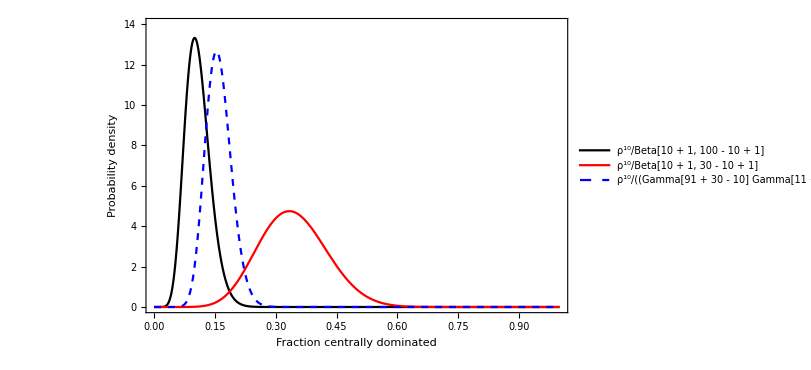

```mathematica
Plot[{(ρ^10 (1-ρ)^(100-10))/Beta[10+1,100-10+1],(ρ^10 (1-ρ)^(30-10))/Beta[10+1,30-10+1],(ρ^10 (1-ρ)^(100-10)ρ^10 (1-ρ)^(30-10))/((Gamma[91+30-10] Gamma[11+10])/Gamma[102+30])},{ρ,0,1},Frame->True,PlotRange->{0,14},FrameLabel->{"Fraction centrally dominated","Probability density"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->600,
PlotStyle->{Black,Red,Directive[Blue,Dashed]},
PlotLegends->{"ρ^10/Beta[10 + 1, 100 - 10 + 1]","ρ^10/Beta[10 + 1, 30 - 10 + 1]","ρ^10/((Gamma[91 + 30 - 10] Gamma[11 + 10])/Gamma[102 + 30])"}]
```

The posterior probability distribution for the observation  that 10/30 X-ray selected clusters are centrally-dominated. The red  line uses a uniform prior distribution for this fraction; the dashed line uses the prior derived from an assumed previous sample in which 10 out of 100 clusters had dominant central members. The black curve shows the distribution for this earlier sample.

### Example

```mathematica
Plot[{(ρ^10 (1-ρ)^(100-10))/Beta[10+1,100-10+1],(ρ^10 (1-ρ)^(30-10))/Beta[10+1,30-10+1],(ρ^10 (1-ρ)^(100-10)ρ^10 (1-ρ)^(30-10))/((Gamma[91+30-10] Gamma[11+10])/Gamma[102+30])},{ρ,0,1},Frame->True,PlotRange->{0,14},FrameLabel->{"Fraction centrally dominated","Probability density"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->600,
PlotStyle->{Black,Red,Directive[Blue,Dashed]},
PlotLegends->{"ρ^10/Beta[10 + 1, 100 - 10 + 1]","ρ^10/Beta[10 + 1, 30 - 10 + 1]","ρ^10/((Gamma[91 + 30 - 10] Gamma[11 + 10])/Gamma[102 + 30])"}]
```

-Graphics-

The figure makes clear that the data are not really sufficient to alter our prior very much. For example, there is only a 10~per cent chance that the centrally-dominant fraction exceeds even 0.2; and indeed we see that the possibility of it being as high as 33% is completely negligible. Our X-ray clusters differ markedly from the general population.

### Example

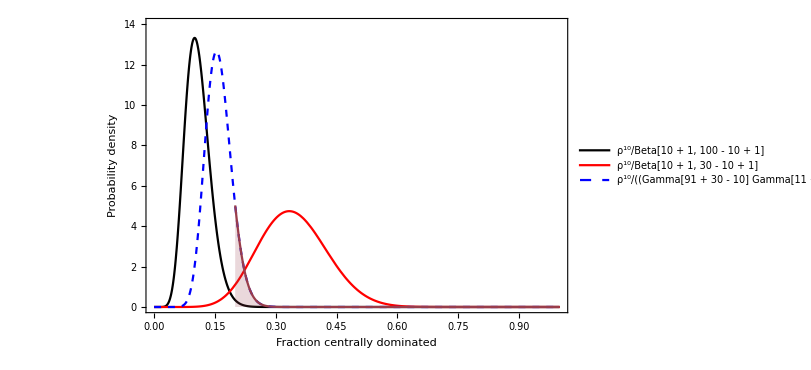

```mathematica
Show[{Plot[{(ρ^10 (1-ρ)^(100-10))/Beta[10+1,100-10+1],(ρ^10 (1-ρ)^(30-10))/Beta[10+1,30-10+1],(ρ^10 (1-ρ)^(100-10)ρ^10 (1-ρ)^(30-10))/((Gamma[91+30-10] Gamma[11+10])/Gamma[102+30])},{ρ,0,1},Frame->True,PlotRange->{0,14},FrameLabel->{"Fraction centrally dominated","Probability density"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->600,
PlotStyle->{Black,Red,Directive[Blue,Dashed]},
PlotLegends->{"ρ^10/Beta[10 + 1, 100 - 10 + 1]","ρ^10/Beta[10 + 1, 30 - 10 + 1]","ρ^10/((Gamma[91 + 30 - 10] Gamma[11 + 10])/Gamma[102 + 30])"}],
Plot[(ρ^10 (1-ρ)^(100-10)ρ^10 (1-ρ)^(30-10))/((Gamma[91+30-10] Gamma[11+10])/Gamma[102+30]),{ρ,0.2,1},Frame->True,Filling->0]}]
```

```mathematica
NIntegrate[(ρ^10 (1-ρ)^(100-10)ρ^10 (1-ρ)^(30-10))/(Gamma[91+30-10] Gamma[11+10])/Gamma[102+30],{ρ,0.2,1}]
```

0.103948

## Geometric Distribution

The geometric distribution gives the probability that the first occurrence of success requires k independent trials, each with success probability p. If the probability of success on each trial is p, then the probability that the k-th trial (out of k trials) is the first success is for k=1,2,3,...

```mathematica
equation[𝒻[X==k,p]==p(1-p)^(k-1)]
```

𝒻(X==k,p)==p (1-p)^(k-1)

The mean (expectation value) is

```mathematica
equation["E"[X]==1/p]
```

E(X)==1/p

The variance  is

```mathematica
equation[var[X]==(1-p)/p^2]
```

var(X)==(1-p)/p^2

### P.M.F. - probability mass function and C.D.F. Cumulative distribution function

𝒻(k; ρ)=𝒫(X=k)=(ρ(1-ρ))^(k-1)

F(k; ρ)=𝒫(X=k)=1-(1-ρ)^k

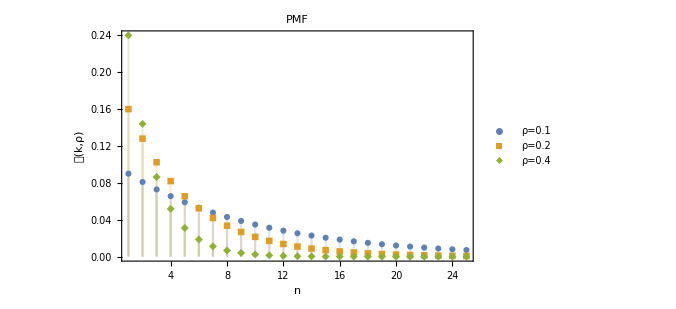
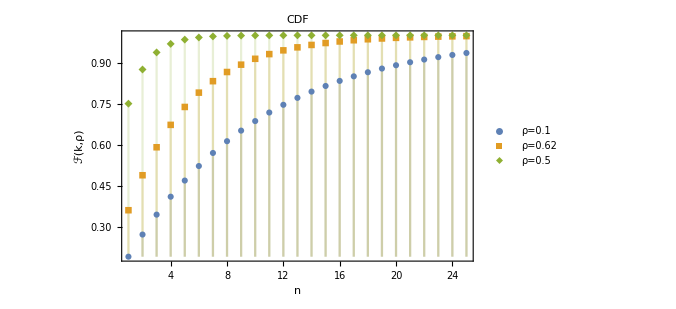
-Graphics- | -Graphics-

```mathematica
Grid[{{DiscretePlot[Evaluate@Table[PDF[GeometricDistribution[p],k],{p,{0.1,0.2,0.4}}],{k,25},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,PlotRange->All,PlotMarkers->Automatic,
PlotLabel->"PMF",Frame->True,FrameLabel->{"n", "𝒻(k,ρ)"},PlotLegends->Placed[{"ρ=0.1","ρ=0.2","ρ=0.4"},Below]],
DiscretePlot[Evaluate@Table[CDF[GeometricDistribution[p],k],{p,{0.1,0.2,0.5}}],{k,25},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,PlotRange->All,PlotMarkers->Automatic,PlotLabel->"CDF",
Frame->True,FrameLabel->{"n", "ℱ(k,ρ)"},PlotLegends->Placed[{"ρ=0.1","ρ=0.62","ρ=0.5"},Below]]}},Spacings->2]
```

The term probability mass function is used for discrete random variables.

## Beta Distribution

the beta distribution is the conjugate prior probability distribution for the Bernoulli, binomial, negative binomial and geometric distributions

```mathematica
Row[{equation[𝒻[X==x,α,β]==1/Beta[α,β] x^(α-1)(1-x)^(β-1)],Spacer[20],"with",Spacer[20],equation[Beta[α,β]==Gamma[α+β]/(Gamma[α]Gamma[β])]}]
```

𝒻(X==x,α,β)==(x^(α-1) (1-x)^(β-1))/αβwithαβ==(α+β)/(α β)

where Γ is the gamma function and B is the Beta function, which is the normalizing constant to  ensure that f is a probability density function

```mathematica
equationNoBox["(∫_0)^1x^(α - 1)(1-x)^(β - 1)ⅆx"==Beta[α,β]==Gamma[α+β]/(Gamma[α]Gamma[β])]
```

(∫_0)^1x^(α - 1)(1-x)^(β - 1)ⅆx==αβ==(α+β)/(α β)

The mean value is

```mathematica
equation["E"[X]==α/(α+β)]
```

E(X)==α/(α+β)

The variance  is

```mathematica
equation[var[X]==(α β)/((α+β)^2(α+β+1))]
```

var(X)==(α β)/((α+β)^2 (α+β+1))

### PDF - probability density function

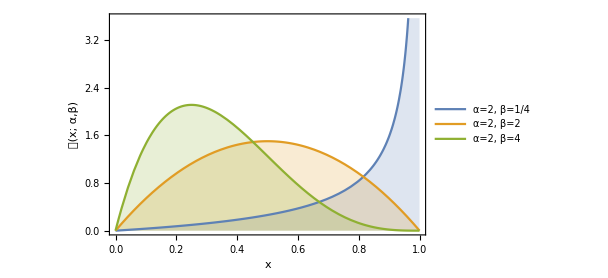
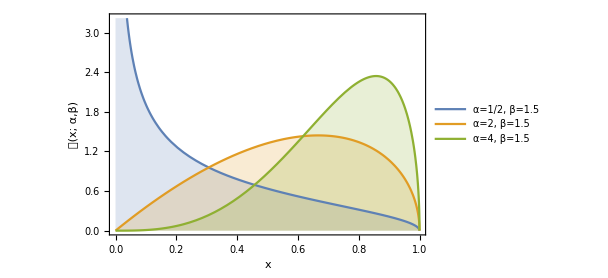
-Graphics- | -Graphics-

```mathematica
Grid[{{Plot[Evaluate@Table[PDF[BetaDistribution[2,β],x],{β,{1/4,2,4}}],{x,0,1},Filling->Axis,Frame->True,FrameLabel->{"x", "𝒫(x; α,β)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450,PlotLegends->{"α=2, β=1/4","α=2, β=2","α=2, β=4"}],Plot[Evaluate@Table[PDF[BetaDistribution[α,1.5],x],{α,{1/2,2,4}}],{x,0,1},Filling->Axis,Frame->True,FrameLabel->{"x", "𝒫(x; α,β)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450,PlotLegends->{"α=1/2, β=1.5","α=2, β=1.5","α=4, β=1.5"}]}},Spacings->2]
```

### CDF - cumulative distribution function

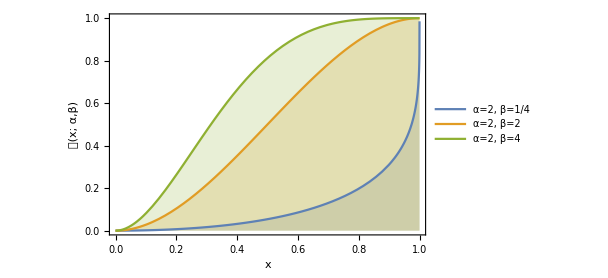
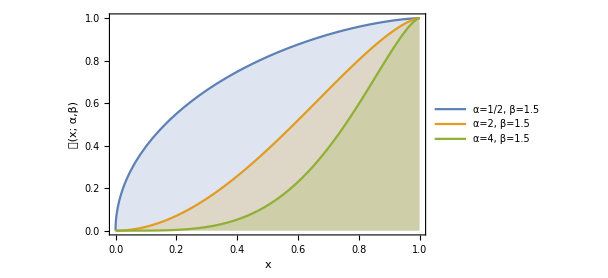
-Graphics- | -Graphics-

```mathematica
Grid[{{Plot[Evaluate@Table[CDF[BetaDistribution[2,β],x],{β,{1/4,2,4}}],{x,0,1},Filling->Axis,Frame->True,FrameLabel->{"x", "𝒫(x; α,β)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450,PlotLegends->{"α=2, β=1/4","α=2, β=2","α=2, β=4"}],Plot[Evaluate@Table[CDF[BetaDistribution[α,1.5],x],{α,{1/2,2,4}}],{x,0,1},Filling->Axis,Frame->True,FrameLabel->{"x", "𝒫(x; α,β)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450,PlotLegends->{"α=1/2, β=1.5","α=2, β=1.5","α=4, β=1.5"}]}},Spacings->2]
```

## The Poisson Distribution

The Poisson distribution derives from the binomial in the limiting case of very rare events and a large number of trials, so that although ρ → 0, N×ρ → (a finite value). Calling this finite mean value μ, the Poisson distribution is

𝒻(n)=μ^n/(n!)ⅇ^-μ

The variance of the Poisson distribution is also μ.

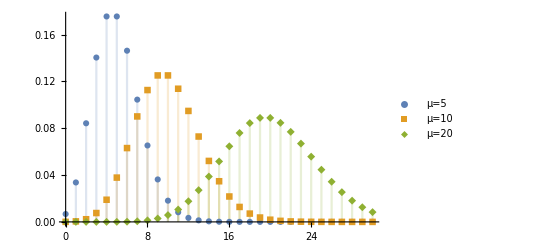

```mathematica
DiscretePlot[Evaluate@Table[PDF[PoissonDistribution[λ],k],{λ,{5,10,20}}],{k,0,30},BaseStyle->{FontSize->14,Font->"Times"},ImageSize->400,PlotRange->All,PlotMarkers->Automatic,PlotLegends->{"μ=5","μ=10","μ=20"}]
```

For higher values of μ the distribution becomes more symmetric.

## The Poisson Distribution

```mathematica
StandardDeviation[PoissonDistribution[μ]]
```

√μ

```mathematica
Skewness[PoissonDistribution[μ]]
```

1/(√μ)

```mathematica
Limit[Skewness[PoissonDistribution[μ]],μ->Infinity]
```

0

## The Poisson Distribution

The sum of Poisson variables is Poisson distributed:

```mathematica
TransformedDistribution[u+v,{u\[Distributed]PoissonDistribution[Subscript[λ, 1]],v\[Distributed]PoissonDistribution[Subscript[λ, 2]]}]
```

PoissonDistribution[λ_1+λ_2]

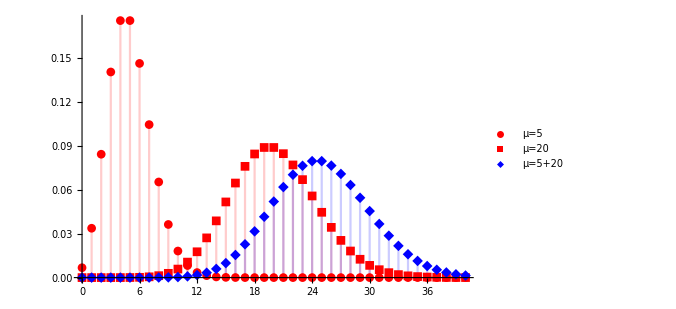

```mathematica
DiscretePlot[{PDF[PoissonDistribution[5], k],PDF[PoissonDistribution[20], k],PDF[PoissonDistribution[5+20], k]}, {k, 0, 40}, BaseStyle -> {FontSize -> 14, Font -> "Times"}, ImageSize -> 500, PlotRange -> All, PlotMarkers -> Automatic,PlotStyle->{Red,Red,Blue},PlotLegends->{"μ=5","μ=20","μ=5+20"}]
```

## The Poisson Distribution

### P.M.F. - probability mass function

𝒻(n; μ)=𝒫(X=n)=∑_(n=0)^k μ^n/(n!)ⅇ^-μ

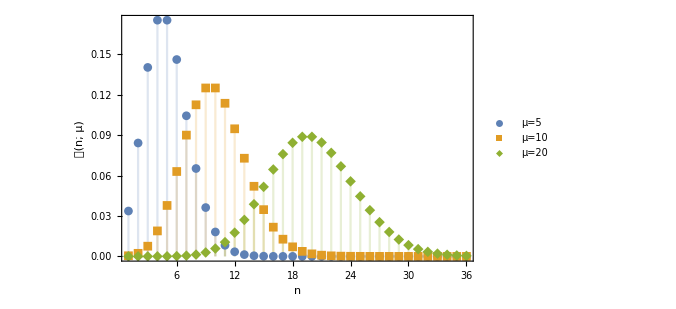

```mathematica
DiscretePlot[Evaluate@Table[PDF[PoissonDistribution[λ],k],{λ,{5,10,20}}],{k,36},PlotRange->All,PlotMarkers->Automatic,Frame->True,FrameLabel->{"n", "𝒻(n; μ)"},BaseStyle->{FontSize->14,Font->"Times"},ImageSize->500,PlotLegends->{"μ=5","μ=10","μ=20"}]
```

## The Poisson Distribution

### CDF - cumulative distribution function

ℱ(k; μ)=𝒫(X≤k)=∑_(n=0)^k μ^n/(n!)ⅇ^-μ

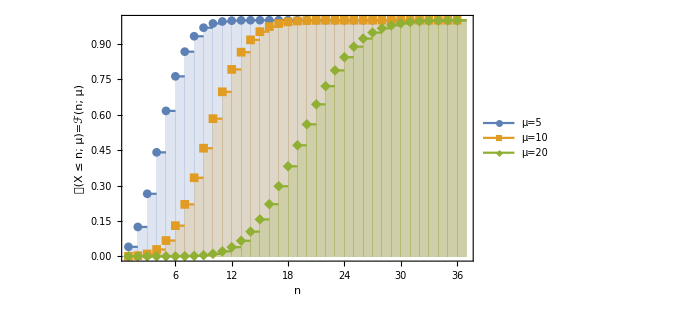

```mathematica
DiscretePlot[Evaluate@Table[CDF[PoissonDistribution[λ],k],{λ,{5,10,20}}],{k,36},ExtentSize->Right,PlotRange->All,PlotMarkers->Automatic,Frame->True,BaseStyle->{FontSize->14,Font->"Times"},ImageSize->500,FrameLabel->{"n", "𝒫(X ≤ n; μ)=ℱ(n; μ)"},PlotLegends->{"μ=5","μ=10","μ=20"}]
```

### Example - Typographical errors

Typographical errors in a book are occurring randomly according to a Poisson process. On 384 pages, 158 errors are counted. Find the distribution of errors per page:

The mean numbers of errors on a page is μ=158/384=0.411458. The probability to find n errors on a single page is 𝒫(n)=0.412^n/(n!)ⅇ^-0.412.

```mathematica
TableForm[Table[{n,(158/384)^n/(n!)ⅇ^(-158/384)//N},{n,0,5}],TableHeadings->{None,{"errors on one page","probability"}}]
```

errors on one page | probability
0 | 0.662683
1 | 0.272666
2 | 0.0560955
3 | 0.00769365
4 | 0.000791404
5 | 0.0000651259

### Example - Typographical errors

```mathematica
TableForm[Table[{n,(158/384)^n/(n!)ⅇ^(-158/384)//N},{n,0,5}],TableHeadings->{None,{"errors on one page","probability"}}]
```

errors on one page | probability
0 | 0.662683
1 | 0.272666
2 | 0.0560955
3 | 0.00769365
4 | 0.000791404
5 | 0.0000651259

The probability of fewer than 2 errors per page is: 𝒫(0)+𝒫(1)=0.663+0.273. This is the cumulative distribution

```mathematica
CDF[PoissonDistribution[158/384],1]//N
```

0.93535

The probability to find 1 or more errors per page is 𝒫(n≥1)=(1-𝒫(0))=1-0.663=0.337. This sometimes also called the survival function.

### Example - Typographical errors

If we are not interested in the number of errors per page, but, e.g. the number of errors in a 50 page booklet, we have to adjust the distribution mean: μ=p×158/384=50×158/384=20.5729.

The probability to find n errors in the booklet is 𝒫(n)=20.5729^n/(n!)ⅇ^-20.5729.

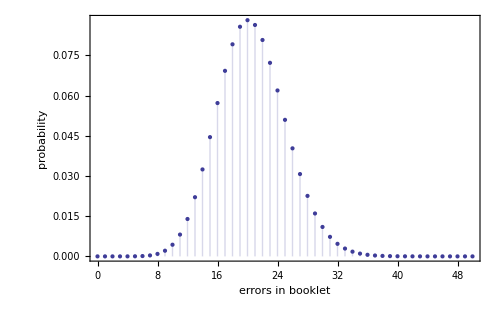

```mathematica
DiscretePlot[20.572916666666664^n/(n!)ⅇ^-20.572916666666664,{n,0,50},Frame->True,BaseStyle->{FontSize->14,Font->"Times"},ImageSize->500,FrameLabel->{"errors in booklet","probability"}]
```

### Example - Scattered rice grains

-Graphics- | Randomly scattered rice on ground: 66 rice grains in 49 squares.

```mathematica
dat={{0,16},{1,14},{2,10},{6,3},{4,1},{5,2},{6,0}};
```

66 rice grains on 49 squares gives λ=N/n=66/49=1.35 grains/square.
𝒫(n)=μ^n/(n!)ⅇ^-μ ⟶ 𝒫(n)=1.35^n/(n!)ⅇ^-1.35

```mathematica
TableForm[Table[{n-1,49*Probability[e==n-1,e\[Distributed]PoissonDistribution[66/49.]],dat[[n,-1]]},{n,1,7}],TableHeadings->{None,{"grains/square","expectation","counted"}}]
```

grains/square | expectation | counted
0 | 12.7417 | 16
1 | 17.1623 | 14
2 | 11.5583 | 10
3 | 5.18944 | 3
4 | 1.74746 | 1
5 | 0.470745 | 2
6 | 0.105678 | 0

### Example - Scattered rice grains

grains/square | expectation | counted
0 | 12.7417 | 16
1 | 17.1623 | 14
2 | 11.5583 | 10
3 | 5.18944 | 3
4 | 1.74746 | 1
5 | 0.470745 | 2
6 | 0.105678 | 0

The probability that a square remains empty is 𝒫(0)=1.35^0/(0!)ⅇ^-1.35=ⅇ^-1.35=0.25924.

### Example - Random distribution

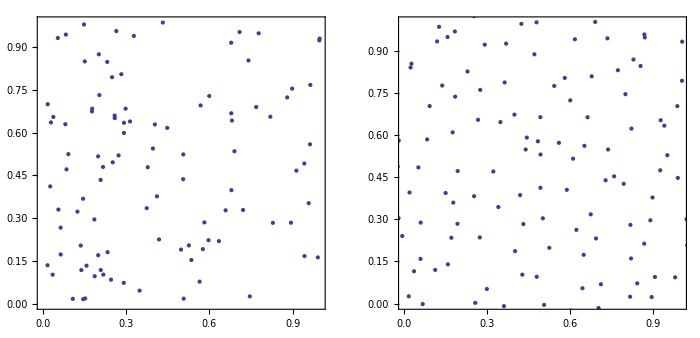

```mathematica
SeedRandom[1234567]
coords=RandomReal[{0,1},{100,2}];
pseudo=Flatten[Table[{x+RandomReal[{-0.05,0.05}],y+RandomReal[{-0.05,0.05}]},{x,0,1,0.1},{y,0,1,0.1}],1];
GraphicsRow[{ListPlot[coords,Frame->True,AspectRatio->1,BaseStyle->{FontSize->14,Font->"Times"},ImageSize->500],ListPlot[pseudo,Frame->True,AspectRatio->1,PlotRange->{{0,1},{0,1}},BaseStyle->{FontSize->14,Font->"Times"},ImageSize->500]},ImageSize->700]
```

In the figure, we placed 100 dots in a unit square. The left panel shows random placement (actually there are no true random number generators on a computer). In the right panel,  we first created a regular grid of 10×10 dots and then slightly shifted them randomly in x and y direction. The left panel shows a much more irregular pattern compared to the  right panel. We see prominent ‘holes’ and ‘clumping’ in the left panel (Poisson clumping).

### Example - Photon statistics

A familiar example of a process obeying Poisson statistics is the number of photons arriving during an integration. The probability of a photon arriving in a fixed interval of time is (often) small (at least at wavelengths shorter than infrared (IR)). The arrivals of successive photons are independent. Thus the conditions necessary for the Poisson distribution are met.

Hence, if the integration over time t of photons arriving at a rate λ has a mean of μ= λt photons, then the fluctuation on this number will be σ=√μ, because we know that the variance is μ (In practice we usually only know the number of photons in a single exposure, rather than the mean number; obviously we can then only estimate the μ.). There are the following limiting cases:

### Example - Photon statistics

Suppose we are detecting our objects with no effective background (either from the sky or the instrument). The observed photons are solely from the objects measured. In this idealized situation, with μ=λ×t, the scatter on μ is (Poisson) σ=√(λ×t). If we integrate more, by simply waiting for more photons, the photon-limited case, 
			σ∝√t, while signal∝t.
Thus, 
			signal/noise∝√t

### Example - Photon statistics

Now suppose our object is barely visible against the sky background. Our signal is still μ=λ×t, but our noise is σ=√(λ_sky×t). The net result is

			S/N∝(λ×t)/(√(λ_sky×t))
Again,
			S/N∝√t

but the sky emission λ_sky×t will be much stronger than the λ×t (sky-limited case). So, in order to achieve the same S/N as in the first case, we need to integrate much longer.

Also note, that the fact that S/N∝√t poses a practical limit on how good an observation can be; half the S/N requires 4 times longer observations, etc..

### Example - Photon statistics

Imagine, we have very bright, photon-limited objects, for which we require very short exposures only, e.g. observation of bright stars or hot dust. Thus, with strong signal and short exposure, the readout noise of the detector (fixed, time-independent, added on top of the signal) may dominate the errors. Calling this fixed error σ_readout:

			S/N∝(λ×t)/σ_readout, or ∝t

### Example - Photon statistics

At the long-wavelength end of the spectrum (sub-millimeter & radio), the photon flux from objects is so strong, that the Poisson statistics of rare events no longer applies! We are in the receiver-limited case; S/N is governed by the receiver sensitivity. We have now such a quantity of photons from the object (photon flux S), that it is the receiver noise which requires the integration:

			S/N∝S/(σ_rec/√t), or ∝√t
for a receiver of thermal noise σ_rec.

## Power law distribution (Pareto distribution)

Take N objects (or events) with measured property (e.g. luminosity) either greater than a value  L or within a bin ⅆL centered on L. With γ as the power-law exponent

N(>L)=K×L^(γ+1)		integral form, N>L, or

ⅆN=(γ+1)×K×L^γ×ⅆL, 	differential form, ⅆN objects in ⅆL.

This is a scale-free or scale-independent distribution, because if 
			𝒻(x)=x^y, then 𝒻(a x)=a^y x^y=const×x^y=const×𝒻(x)  
(definition of scale independence).

Not formally a probability distribution because ∫ⅆN→∞

formally, mean and variance →∞

normally there are physical bounds so that it works

Steep power laws -4 < γ < 0, extending over decades,  occur in astronomy frequently

## Power law distribution (Pareto distribution)

### Example

-Graphics- | Observations of molecular clouds  show an almost universal clump-mass distribution with 

ⅆN/ⅆM∝M^(-1.6...-1.8)

(Kramer et al. 1998)

## Power law distribution (Pareto distribution)

Describing results for objects selected from power-law distributions in terms of means and sigmas becomes very misleading (or wrong). Generally, the slopes of  the power laws are steep and inverse, i.e. there are many more objects with small L than large ⇒ strong bias when objects are drawn from such a parent population.

Astronomical examples:

Salpeter Mass function (IMF)

Clump-mass distribution and mass-size relation for molecular clouds

magnitude or source counts (surface density of objects on the sky)

luminosity functions

primordial fluctuations spectrum

There are always more faint objects, more low-mass or low-luminosity objects than high ⟶γ is invariably negative.

Power-law distributions indicate that something interesting is going on.

## Power law distribution (Pareto distribution)

Pitfalls:

Characterizing by means or variances completely misleading.The Central Limit Theorem fails us badly.

The index!

differential or integral form?

binning: uniform or on a Δlog(L) scale (ⅆ(log(L))=const×L^-1 ⅆL) → index reduced by 1!

Given a fixed range of power law between a and b, the mean can be calculated:

μ=((γ+1)/(γ+2))[(b^(γ+2)-a^(γ+2))/(b^(γ+1)-a^(γ+1))]

The expression breaks down for γ=-1 or -2;

## Power law distribution (Pareto distribution)

### PDF - probability density function

In a looser sense, a power-law probability distribution is a distribution whose density function (or mass function in the discrete case) has the form

𝒻(x)∝L(x) x^-α				BE CAREFUL - DIFFERENT DEFINITON!

For instance, if L(x) is the constant function, then we have a power law that holds for all values of x. In many cases, it is convenient to assume a lower bound x_min from which the law holds. Combining these two cases, and where x is a continuous variable, the power law has the form

𝒻(x)=(α-1)/x_min(x/x_min)^-α

The pre-factor is the normalizing factor. With this distribution, we can now define, e.g. the mean value

⟨𝒻(x)⟩=∫_x_min^∞ x 𝒻(x)ⅆx=(α-1)/(α-2)x_min

## Power law distribution (Pareto distribution)

### PDF - probability density function

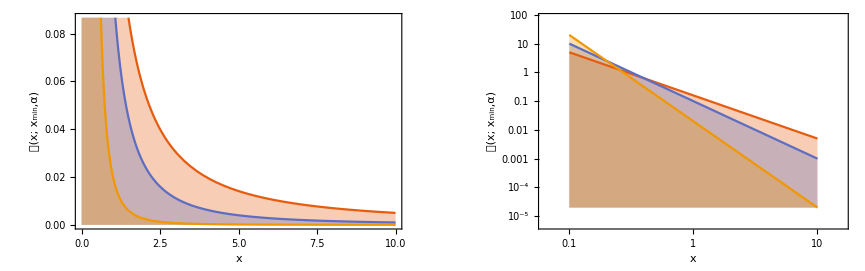
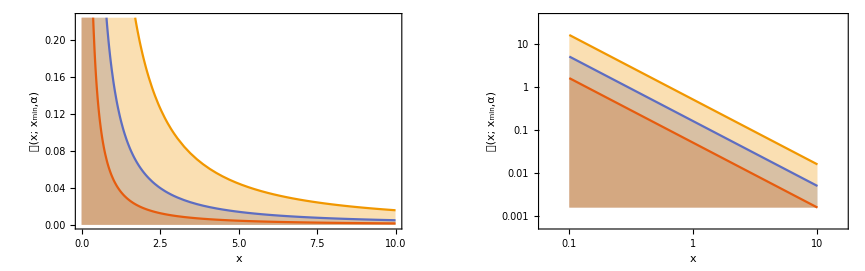
-Graphics- | 
-Graphics- |

```mathematica
Grid[{{GraphicsRow[{Plot[Evaluate@Table[(α-1)/0.1(x/0.1)^-α,{α,{1.5,2,3}}],{x,0,10},Filling->Axis,PlotRange->Automatic,Frame->True,FrameLabel->{"x", "𝒻(x; x_min,α)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->400],LogLogPlot[Evaluate@Table[(α-1)/0.1(x/0.1)^-α,{α,{1.5,2,3}}],{x,0.1,10},Filling->Axis,PlotRange->Automatic,Frame->True,FrameLabel->{"x", "𝒻(x; x_min,α)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->400]}],LineLegend[{ColorData[1][1],ColorData[1][2],ColorData[1][3]},{"α=1.5, x_min=0.1","α=2, x_min=0.1","α=3, x_min=0.1"}]},{GraphicsRow[{Plot[Evaluate@Table[(1.5-1)/xmin(x/xmin)^-1.5,{xmin,{0.01,0.1,1}}],{x,0,10},Filling->Axis,PlotRange->Automatic,Frame->True,FrameLabel->{"x", "𝒻(x; x_min,α)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->400],LogLogPlot[Evaluate@Table[(1.5-1)/xmin(x/xmin)^-1.5,{xmin,{0.01,0.1,1}}],{x,0.1,10},Filling->Axis,PlotRange->Automatic,Frame->True,FrameLabel->{"x", "𝒻(x; x_min,α)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->400]}],LineLegend[{ColorData[1][1],ColorData[1][2],ColorData[1][3]},{"α=1.5, x_min=0.01","α=1.5, x_min=0.1","α=1.5, x_min=1"}]}}]
```

## Power law distribution (Pareto distribution)

### CDF - cumulative distribution function

In general, power - law distributions are plotted on doubly logarithmic axes, which emphasizes the upper tail region.The most convenient way to do this is via the (complementary) cumulative distribution (cdf),

Complementary cumulative distribution function

			ℱ̄(x)=𝒫(X>x)=C∫_x^∞ 𝒻(x)ⅆx=(α-1)/x_min^(-α+1)∫_x^∞ X^-α ⅆX=(x/x_min)^(-α+1)

The regular CDF is then		

			ℱ(x)=𝒫(X≤x)=1-ℱ̄(x)=1-(x/x_min)^(-α+1)

Note that the cdf is also a power-law function, but with a smaller scaling exponent.

## Power law distribution (Pareto distribution)

### CDF - cumulative distribution function

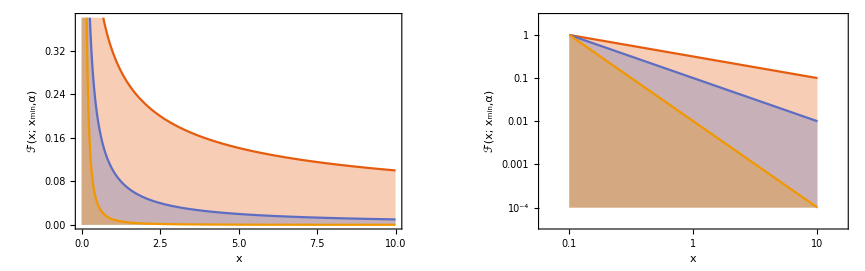
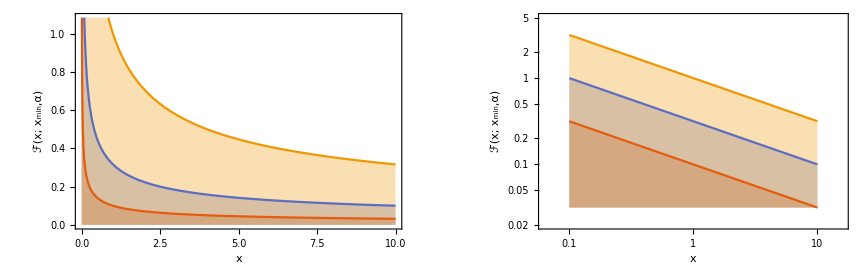
-Graphics- | 
-Graphics- |

```mathematica
Grid[{{GraphicsRow[{Plot[Evaluate@Table[(x/0.1)^(-α+1),{α,{1.5,2,3}}],{x,0,10},Filling->Axis,PlotRange->Automatic,Frame->True,FrameLabel->{"x", "ℱ̄(x; x_min,α)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->400],LogLogPlot[Evaluate@Table[(x/0.1)^(-α+1),{α,{1.5,2,3}}],{x,0.1,10},Filling->Axis,PlotRange->Automatic,Frame->True,FrameLabel->{"x", "ℱ̄(x; x_min,α)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->400]}],LineLegend[{ColorData[1][1],ColorData[1][2],ColorData[1][3]},{"α=1.5, x_min=0.1","α=2, x_min=0.1","α=3, x_min=0.1"}]},{GraphicsRow[{Plot[Evaluate@Table[(x/xmin)^(-1.5+1),{xmin,{0.01,0.1,1}}],{x,0,10},Filling->Axis,PlotRange->Automatic,Frame->True,FrameLabel->{"x", "ℱ̄(x; x_min,α)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->400],LogLogPlot[Evaluate@Table[(x/xmin)^(-1.5+1),{xmin,{0.01,0.1,1}}],{x,0.1,10},Filling->Axis,PlotRange->Automatic,Frame->True,FrameLabel->{"x", "ℱ̄(x; x_min,α)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->400]}],LineLegend[{ColorData[1][1],ColorData[1][2],ColorData[1][3]},{"α=1.5, x_min=0.01","α=1.5, x_min=0.1","α=1.5, x_min=1"}]}}]
```

## Gaussian (Normal) distribution

The Binomial and the Poisson distribution both tend to the Gaussian distribution (large N in case of Binomial, large μ in case of Poisson). The univariate Gaussian (Normal) distribution is:

```mathematica
equation[𝒻[n,μ,σ]=="1/(σ SqrtBox[2  π])""exp"parens[-(x-μ)^2/(2 σ^2)]]
```

𝒻(n,μ,σ)==1/(σ SqrtBox[2  π]) exp (-(x-μ)^2/(2 σ^2))

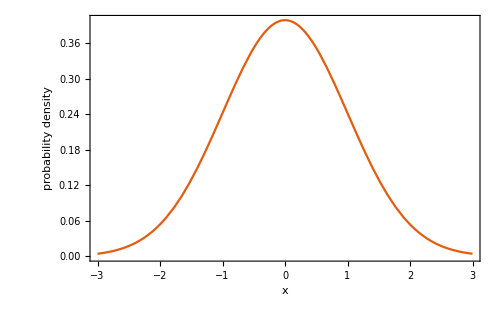

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-3,3},Frame->True,Axes->False,BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,FrameLabel->{x,"probability density"}]
```

## Gaussian (Normal) distribution

### Properties

It is symmetric around the point x=μ which is at the same time the mode, the median and the mean of the distribution.

It has two inflection points (where the second derivative of 𝒫 is zero and changes sign), located one standard deviation away from the mean, namely at x = μ−σ and x = μ+ σ.

The area under the curve is unity (because of the normalizing factor 1/(σ √(2π))

```mathematica
Integrate[Exp[-(x-μ)^2/(2 σ^2)],{x,-∞,∞},Assumptions:>σ>0]
```

√(2 π) σ

The Full Width at Half Maximum (FWHM) is the width of a spectrum curve measured between those points on the y-axis which are half the maximum amplitude (log is the natural logarithm!)

```mathematica
equationInvBox[FWHM==2 √(2Log[2])σ"≈ 2.335σ"]
```

FWHM==2 √(2 log(2)) σ ≈ 2.335σ

```mathematica
Solve[1/2==Exp[-(x-μ)^2/(2 σ^2)],x,Reals][[All,1,2]]//Differences
```

{2 √(σ^2) √(2 Log[2])}

## Gaussian (Normal) distribution

### Properties

The mean value of the Normal distribution is μ.

The variance is σ^2.

## Gaussian (Normal) distribution

### Properties

For a very large sample size N, the discrete Binomial distribution tends to the continuous Normal distribution with mean μ=N×p and variance σ^2=N×p×(1-p).

```mathematica
equation[Prparens[n]=="1/(σ SqrtBox[2  π])""exp"parens[-(n-μ)^2/(2 σ^2)]]
```

Pr(n)==1/(σ SqrtBox[2  π]) exp (-(n-μ)^2/(2 σ^2))

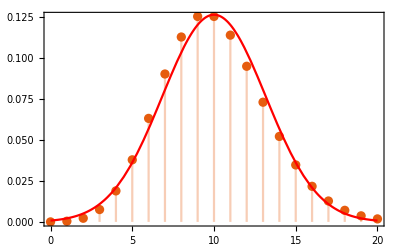
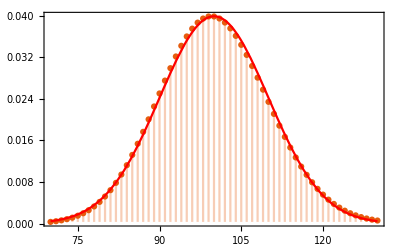
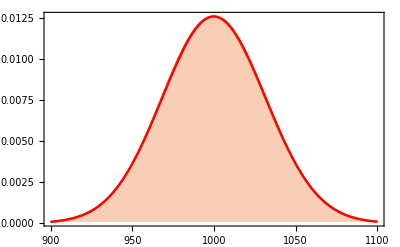
-Graphics-N=10 | -Graphics-N=100 | -Graphics-N=1000

```mathematica
Grid[{{Labeled[Show[DiscretePlot[PDF[PoissonDistribution[10^1],k],{k,0,20},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->400,PlotRange->All],Plot[PDF[NormalDistribution[10^1,Sqrt[10^1]],x],{x,0,20},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,PlotStyle->Directive[Thick,Red]]],"N=10",Top],
Labeled[Show[DiscretePlot[PDF[PoissonDistribution[10^2],k],{k,70,130},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->400,PlotRange->All],Plot[PDF[NormalDistribution[10^2,Sqrt[10^2]],x],{x,70,130},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,PlotStyle->Directive[Thick,Red]]],"N=100",Top],
Labeled[Show[{DiscretePlot[PDF[PoissonDistribution[10^3],k],{k,900,1100},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->400,PlotRange->All],Plot[PDF[NormalDistribution[10^3,Sqrt[10^3]],x],{x,900,1100},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,PlotStyle->Directive[Thick,Red]]}],"N=1000",Top]}},Spacings->2]
```

## Gaussian (Normal) distribution

### PDF - probability density function

```mathematica
equation[𝒻[x";"μ,σ]=="1/(σ SqrtBox[2  π])""exp"parens[-(x-μ)^2/(2 σ^2)]]
```

𝒻(x ; μ,σ)==1/(σ SqrtBox[2  π]) exp (-(x-μ)^2/(2 σ^2))

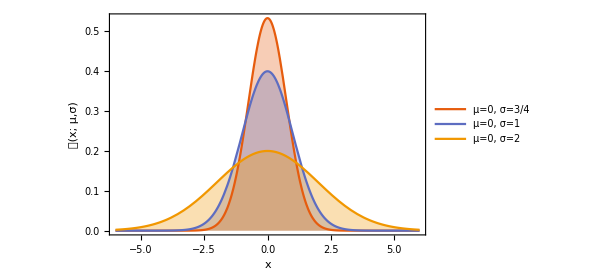
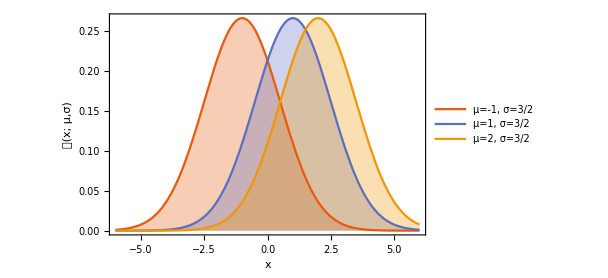
-Graphics- | -Graphics-

```mathematica
Grid[{{Plot[Evaluate@Table[PDF[NormalDistribution[0,σ],x],{σ,{.75,1,2}}],{x,-6,6},Filling->Axis,PlotRange->All,Frame->True,FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450,PlotLegends->{"μ=0, σ=3/4","μ=0, σ=1","μ=0, σ=2"}],Plot[Evaluate@Table[PDF[NormalDistribution[μ,1.5],x],{μ,{-1,1,2}}],{x,-6,6},Filling->Axis,PlotRange->All,Frame->True,FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450,PlotLegends->{"μ=-1, σ=3/2","μ=1, σ=3/2","μ=2, σ=3/2"}]}},Spacings->2]
```

## Gaussian (Normal) distribution

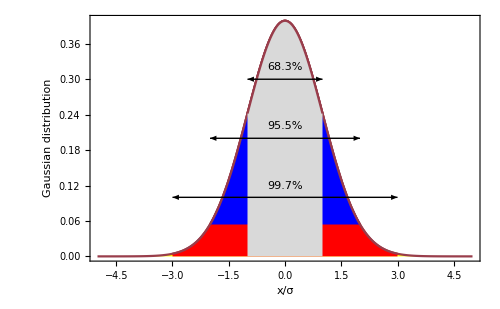
x/σ | one tail | both tails | between tails
0. | 50. | 100. | 0.
0.5 | 30.8538 | 61.7075 | 38.2925
1. | 15.8655 | 31.7311 | 68.2689
1.5 | 6.68072 | 13.3614 | 86.6386
2. | 2.27501 | 4.55003 | 95.45
2.5 | 0.620967 | 1.24193 | 98.7581
3. | 0.13499 | 0.26998 | 99.73
3.5 | 0.0232629 | 0.0465258 | 99.9535
4. | 0.00316712 | 0.00633425 | 99.9937
4.5 | 0.000339767 | 0.000679535 | 99.9993
5. | 0.0000286652 | 0.0000573303 | 99.9999Percentage area under the Gaussian curve | -Graphics-

```mathematica
Grid[{{Labeled[TableForm[Table[{m,100NIntegrate[PDF[NormalDistribution[],x],{x,-∞,-m}],100 2NIntegrate[PDF[NormalDistribution[],x],{x,-∞,-m}],100 NIntegrate[PDF[NormalDistribution[],x],{x,-m,m}]}//N,{m,0,5,0.5}],TableHeadings->{None,Style[#,Bold]&/@{"x/σ","one tail","both tails","between tails"}}],Style["Percentage area under the Gaussian curve",Bold],Top],
Show[{Plot[PDF[NormalDistribution[],x],{x,-5,5},ImageSize->500,
Frame->True,Axes->False,FrameLabel->{"x/σ","Gaussian distribution"},Filling->Axis,FillingStyle->Yellow,PlotRange->{0,0.4},BaseStyle->{FontSize->16,Font->"Times"}],
Plot[PDF[NormalDistribution[],x],{x,-3,3},ImageSize->500,BaseStyle->{FontSize->16,Font->"Times"},
Frame->True,Axes->False,Filling->Axis,FillingStyle->Red],
Plot[PDF[NormalDistribution[],x],{x,-2,2},ImageSize->500,BaseStyle->{FontSize->16,Font->"Times"},
Frame->True,Axes->False,Filling->Axis,FillingStyle->Blue],
Plot[PDF[NormalDistribution[],x],{x,-1,1},ImageSize->500,BaseStyle->{FontSize->16,Font->"Times"},
Frame->True,Axes->False,Filling->Axis,FillingStyle->LightGray,PlotRange->{0,0.4}
]},Epilog->{Thick,Arrowheads[{-.05,.05}], Arrow[{{-2,0.2},{2,0.2}}],Text["95.5%",{0,0.22}],
 Arrow[{{-1,0.3},{1,0.3}}],Text["68.3%",{0,0.32}],
 Arrow[{{-3,0.1},{3,0.1}}],Text["99.7%",{0,0.12}]

}]}},Spacings->2
]
```

## Gaussian (Normal) distribution

### CDF - cumulative distribution function

```mathematica
equation[ℱ[k";"μ,σ]==Pr parens[X≤k]==∫_(-∞)^k "1/(σ SqrtBox[2  π])""exp"parens[-(x-μ)^2/(2 σ^2)]ⅆx=1/2 parens[1+TraditionalForm@Erf[(k-μ)/(√2 σ)]]]
```

ℱ(k ; μ,σ)==Pr(X≤k)==∫_(-∞)^k 1/(σ SqrtBox[2  π]) exp (-(x-μ)^2/(2 σ^2))ⅆx=1/2 (1+erf((k-μ)/(√2 σ)))

## Gaussian (Normal) distribution

### CDF - cumulative distribution function

```mathematica
Assuming[σ>0,∫_(-∞)^k (ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)ⅆx]
```

1/2 (erf((k-μ)/(√2 σ))+1)

```mathematica
CDF[NormalDistribution[μ,σ],x]
```

1/2 erfc((μ-x)/(√2 σ))

The complementary error function erfc(z) is given by erfc(z)=1-erf(z). The error function erf(z) is the integral of the (normalized) Gaussian distribution, given by erf(z)=2/(√π)∫_0^z e^(-t^2)dt.

## Gaussian (Normal) distribution

### CDF - cumulative distribution function

```mathematica
equation[ℱ[k";"μ,σ]==Pr parens[X≤k]==∫_(-∞)^k "1/(σ SqrtBox[2  π])""exp"parens[-(x-μ)^2/(2 σ^2)]ⅆx=1/2 parens[1+TraditionalForm@Erf[(k-μ)/(√2 σ)]]]
```

ℱ(k ; μ,σ)==Pr(X≤k)==∫_(-∞)^k 1/(σ SqrtBox[2  π]) exp (-(x-μ)^2/(2 σ^2))ⅆx=1/2 (1+erf((k-μ)/(√2 σ)))

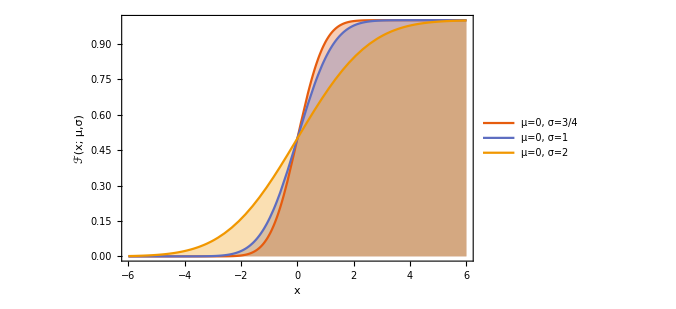
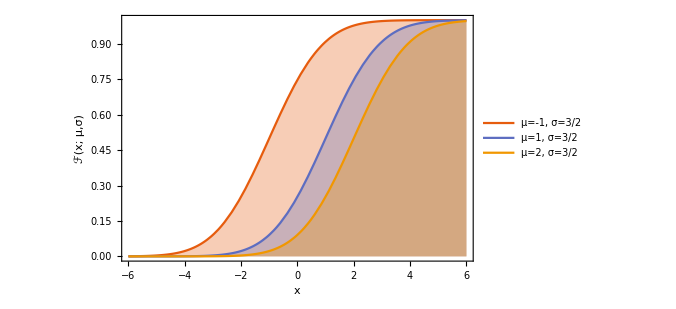
-Graphics- | -Graphics-

```mathematica
Grid[{{Plot[Evaluate@Table[CDF[NormalDistribution[0,σ],x],{σ,{.75,1,2}}],{x,-6,6},Filling->Axis,PlotRange->All,Frame->True,FrameLabel->{"x", "ℱ(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,PlotLegends->Placed[{"μ=0, σ=3/4","μ=0, σ=1","μ=0, σ=2"},Below]],Plot[Evaluate@Table[CDF[NormalDistribution[μ,1.5],x],{μ,{-1,1,2}}],{x,-6,6},Filling->Axis,PlotRange->All,Frame->True,FrameLabel->{"x", "ℱ(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,PlotLegends->Placed[{"μ=-1, σ=3/2","μ=1, σ=3/2","μ=2, σ=3/2"},Below]]}},Spacings->2]
```

## Gaussian (Normal) distribution

### Error function

```mathematica
Row[{equationNoBox[Erf[z]==2/(√π)∫_0^z "exp"[-t^2]ⅆt],",",Spacer[50],equationNoBox[Erfc[z]==1-Erf[z]]}]
```

erf(z)==(2 ∫_0^z exp(-t^2)ⅆt)/(√π),erfc(z)==1-erf(z)

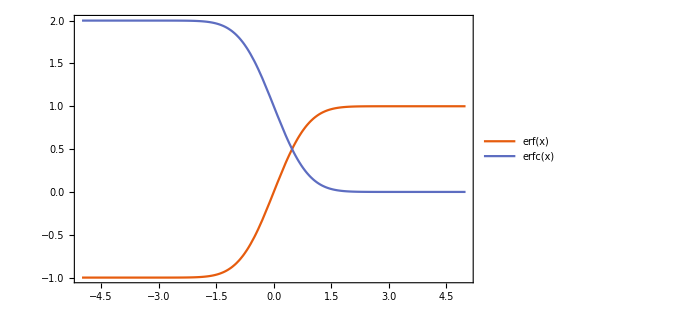

```mathematica
Plot[{Erf[x],Erfc[x]},{x,-5,5},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,PlotLegends->"Expressions",Axes->True]
```

## Gaussian (Normal) distribution

### Error function

Be careful what definition is actually implied, sometimes erf(μ) is interpreted as 2/(√π)∫_-μ^(,μ) e^(-t^2)dt.

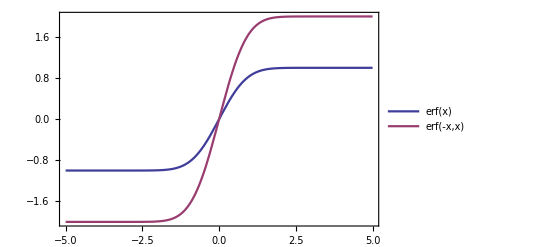

```mathematica
Plot[{Erf[x],Erf[-x,x]},{x,-5,5},PlotLegends->"Expressions",BaseStyle->{FontSize->16,Font->"Times"},ImageSize->400,Axes->True]
```

The error function expressed in terms of a series expansion:

```mathematica
Series[Erf[x],{x,0,10}]
```

(2 x)/(√π)-(2 x^3)/(3 √π)+x^5/(5 √π)-x^7/(21 √π)+x^9/(108 √π)+O[x]^11

## Gaussian (Normal) distribution

### Comparing draws from different (normal) distributions

Suppose a student sits 2 exams, getting 55 in a verbal test and 60 in a numerical reasoning test. The class scores for each exam are normally distributed. For the verbal test, the mean is 50 and standard deviation 5; for the numerical test, the mean is 50 and standard deviation is 12. 
Now it is plain to see that the student did above average for each test, and did better at numerical reasoning. How did this student perform relative to everyone else? We can answer this by calculating the z-score.

```mathematica
equation[Z==(observation-mean)/SD]
```

Z==(observation-mean)/SD

## Gaussian (Normal) distribution

### Comparing draws from different (normal) distributions

```mathematica
equation[Z==(observation-mean)/SD]
```

Z==(observation-mean)/SD

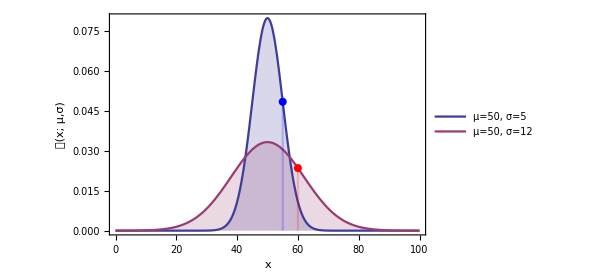
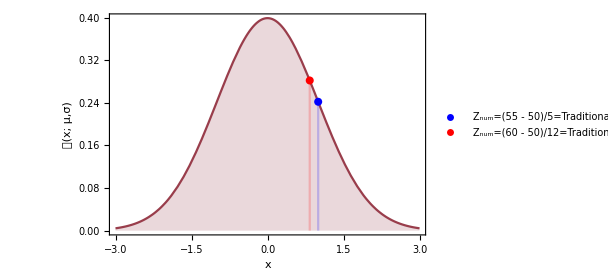

```mathematica
Row[{Show[{
Plot[{PDF[NormalDistribution[50,5],x],PDF[NormalDistribution[50,12],x]},{x,0,100},Filling->Axis,PlotRange->All,Frame->True,FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450,PlotLegends->Placed[{"μ=50, σ=5","μ=50, σ=12"},Above]],DiscretePlot[PDF[NormalDistribution[50,5],x],{x,{55}},Filling->0,PlotStyle->Blue,FillingStyle->Directive[Blue,Thick],PlotRange->All,Frame->True,FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450],
DiscretePlot[PDF[NormalDistribution[50,12],x],{x,{60}},Filling->0,PlotStyle->Red,FillingStyle->Directive[Red,Thick],PlotRange->All,Frame->True,FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450]}],Spacer[40],Show[{Plot[PDF[NormalDistribution[0,1],x],{x,-3,3},Filling->Axis,PlotRange->All,Frame->True,FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450],Legended[DiscretePlot[PDF[NormalDistribution[0,1],x],{x,{1}},Filling->0,PlotRange->All,Frame->True,PlotStyle->Blue,FillingStyle->Directive[Blue,Thick],FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450],Placed[PointLegend[{Blue},{"Z_num=(55 - 50)/5=TraditionalForm`1"}],Above]],
Legended[DiscretePlot[PDF[NormalDistribution[0,1],x],{x,{0.833333}},Filling->0,PlotRange->All,Frame->True,PlotStyle->Red,FillingStyle->Directive[Red,Thick],FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450],Placed[PointLegend[{Red},{"Z_num=(60 - 50)/12=TraditionalForm`0.833"}],Above]]}]}]
```

## Standardization with Z scores

```mathematica
equation[Z==(observation-mean)/SD]
```

Z==(observation-mean)/SD

standardized (Z) score of an observation is the number of standard deviations it falls above or below the mean

Z score of mean = 0

unusual observation: |Z| > 2

defined for distributions of any shape

## Standardization with Z scores

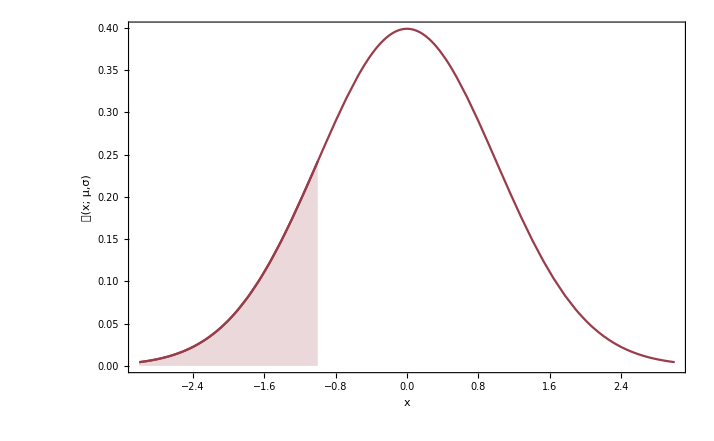
-Graphics- | 1. when the distribution is normal, Z scores can be used to calculate percentiles

2. percentile is the percentage of an observations that falls below a given data point

3. graphically, percentile is the area below the probability distribution curve to the left of that observation (sometimes called P NORM)

## Standardization with Z scores

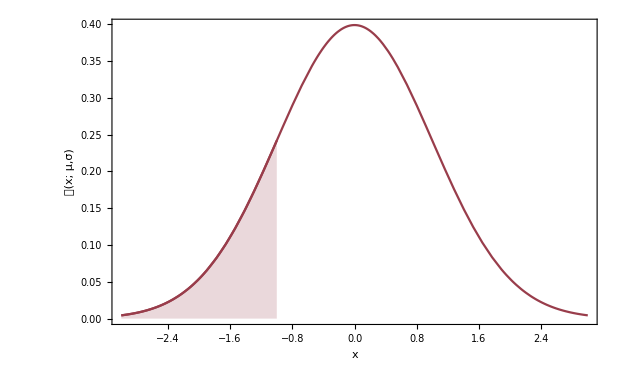
-Graphics- | Computing Z scores with R

-Graphics-

Computing Z scores with tabulated values
-Graphics-

Computing Z scores with Mathematica

```mathematica
CDF[NormalDistribution[0,1],-1.]
```

0.158655

Alternatively, use a web applet: e.g. http://bitly.com/dist_calc or http://vassarstats.net/tabs.html

## Standardization with Z scores

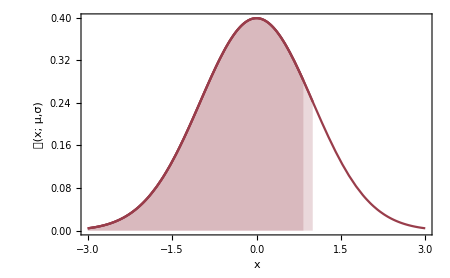

```mathematica
Show[{Plot[PDF[NormalDistribution[],x],{x,-3,3},Filling->None,PlotRange->All,Frame->True,FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450],Plot[PDF[NormalDistribution[],x],{x,-3,0.8333},Filling->Axis,PlotRange->All,Frame->True,FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450],
Plot[PDF[NormalDistribution[],x],{x,-3,1},Filling->Axis,PlotRange->All,Frame->True,FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450]}]
```

Given our earlier example, the exam results expressed in percentiles are

```mathematica
CDF[NormalDistribution[0, 1],0.833]
```

0.797578

```mathematica
CDF[NormalDistribution[0, 1],1.]
```

0.841345

The student performed better than 84% of all the students in the verbal exam and better than 79% in the numerical exam.

## Standardization with Z scores

### Example: Weather conditions

Radio observations require dry atmospheric conditions. Suppose the average perceptible water vapor (PWV) at an astronomical observatory site is 1 mm with a standard deviation of 0.3. Suppose the PWV statistics follow closely a Normal distribution. How dry is the atmosphere at the best 10% of observing days?

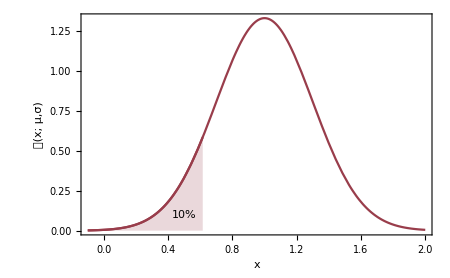

```mathematica
Show[{Plot[PDF[NormalDistribution[1,0.3],x],{x,-0.1,2},Filling->None,PlotRange->All,Frame->True,FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450,Epilog->Text["10%",{0.5,0.1}]],
Plot[PDF[NormalDistribution[1,0.3],x],{x,-.1,InverseCDF[NormalDistribution[1,0.3],0.1]},Filling->Axis,PlotRange->All,Frame->True,FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450]}]
```

## Standardization with Z scores

### Example: Weather conditions

```mathematica
Show[{Plot[PDF[NormalDistribution[1,0.3],x],{x,-0.1,2},Filling->None,PlotRange->All,Frame->True,FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450,Epilog->Text["10%",{0.5,0.1}]],
Plot[PDF[NormalDistribution[1,0.3],x],{x,-.1,InverseCDF[NormalDistribution[1,0.3],0.1]},Filling->Axis,PlotRange->All,Frame->True,FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450]}]
```

-Graphics-

In other words, at which value of x is the c.d.f. equal to 0.1?

```mathematica
InverseCDF[NormalDistribution[1,0.3],0.1]
```

0.615535

10% of the time, the atmospheric conditions will be such that pwv<0.62 mm.

### Example: Weather conditions

Another way to solve this problem is by using tabulated values of the normalized c.d.f.. In the table below,we show a part of such a table, where each column and row represents the CDF for one Z score (row: 1. decimal, col: 2nd decimal)

```mathematica
TableForm[Table[If[{x,y}=={-1.3,0.01}||{x,y}=={-1.3,0.02},Style[#,Bold,Background->Orange],#]&@CDF[NormalDistribution[0,1],x+y],{x,-1.6,-1,.1},{y,0,0.04,.01}],TableHeadings->{Range[-1.6,-1,.1],Range[0,0.04,.01]}]
```

| 0. | 0.01 | 0.02 | 0.03 | 0.04
-1.6 | 0.0547993 | 0.0559174 | 0.0570534 | 0.0582076 | 0.0593799
-1.5 | 0.0668072 | 0.0681121 | 0.0694366 | 0.0707809 | 0.072145
-1.4 | 0.0807567 | 0.0822644 | 0.0837933 | 0.0853435 | 0.086915
-1.3 | 0.0968005 | 0.0985253 | 0.100273 | 0.102042 | 0.103835
-1.2 | 0.11507 | 0.117023 | 0.119 | 0.121 | 0.123024
-1.1 | 0.135666 | 0.137857 | 0.140071 | 0.14231 | 0.144572
-1. | 0.158655 | 0.161087 | 0.163543 | 0.166023 | 0.168528

Since we don’t know the Z score we use the table to solve the inverse problem:

			Z=?=(X-μ)/σ=(X-1)/0.3
The given CDF value is 0.1. The corresponding Z score is between -1.31 and -1.32 (highlighted values in table). Therefore
			Z=-1.315=(X-μ)/σ=(X-1)/0.3  ⇒  -1.315=(X-1)/0.3⇒X=0.6055

## The Central Limit Theorem

The true importance of the Gaussian distribution and its dominant position in experimental science, stems from the Central Limit Theorem. A non-rigorous statement of this is as follows.

Form averages M_n from repeatedly drawing n samples from a population x_i with finite mean μ, variance σ^2. Then the distribution of

(M_n-μ)/(σ/√n)⟶ Gaussian distribution

with mean 0, variance 1, as n→∞.

This is remarkable!

## The Central Limit Theorem

It says that averaging will produce a Gaussian distribution of results - no matter the shape of distribution from which the sample is drawn.

Errors on averaged samples will always look `Gaussian’.

The Central Limit Theorem shapes our entire view of experimentation ⇒ error language of sigmas, describing tails of Gaussian distributions.

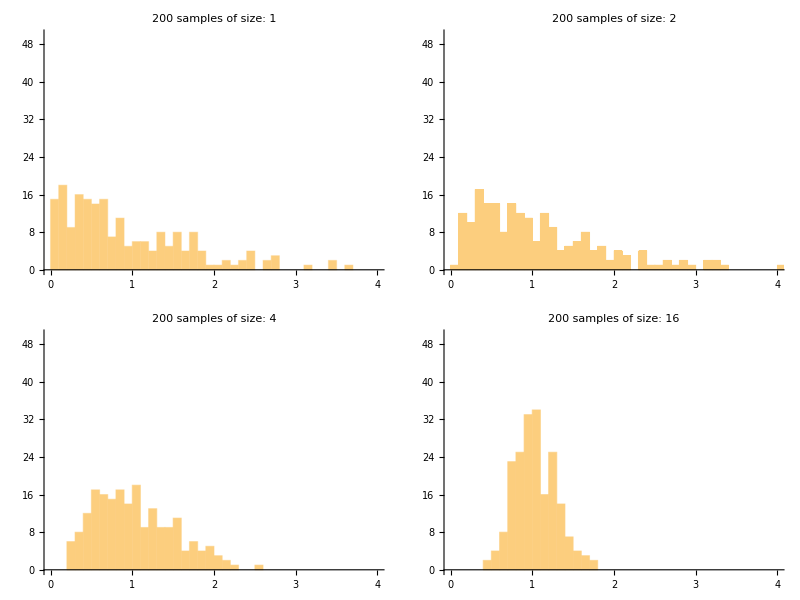

```mathematica
sampleMean[samplesize_,numOfSamples_]:=Table[Mean[RandomVariate[ExponentialDistribution[1],samplesize]],{numOfSamples}];
Grid[{{Histogram[sampleMean[1,200],{.1},PlotRange->{{0,4},{0,50}},PlotLabel->"200 samples of size: 1",BaseStyle->{FontSize->16,Font->"Times"},ImageSize->400,AspectRatio->0.3],
Histogram[sampleMean[2,200],{.1},PlotRange->{{0,4},{0,50}},PlotLabel->"200 samples of size: 2",BaseStyle->{FontSize->16,Font->"Times"},ImageSize->400,AspectRatio->0.3]},{Histogram[sampleMean[4,200],{.1},PlotRange->{{0,4},{0,50}},PlotLabel->"200 samples of size: 4",BaseStyle->{FontSize->16,Font->"Times"},ImageSize->400,AspectRatio->0.3],Histogram[sampleMean[16,200],{.1},PlotRange->{{0,4},{0,50}},PlotLabel->"200 samples of size: 16",BaseStyle->{FontSize->16,Font->"Times"},ImageSize->400,AspectRatio->0.3]}}]
```

Histograms of 200 values drawn from an exponential distribution: averages of 1,2,4, 16.

## Example - CLT

Credits: Dr. Mine Çetinkaya-Rundel, Duke University

Suppose my iPod has 3,000 songs. The histogram below shows the distribution of the lengths of these songs. We also know that, for this iPod, the mean length is 3.45 minutes and the standard deviation is 1.63 minutes. Calculate the probability that a randomly selected song lasts more than 5 minutes.

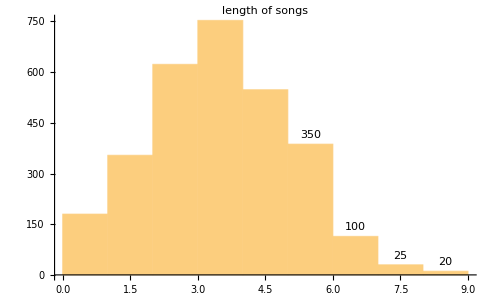
-Graphics- | X = length of one song
Pr(X>s)=(350+100+25+20+5)/3000=500/3000=0.166667

## Example - CLT 2

Credits: Dr. Mine Çetinkaya-Rundel, Duke University

I’m about to take a trip to visit my parents and the drive is 6 hours. I make a random playlist of 100 songs. What is the probability that my playlist lasts the entire drive?

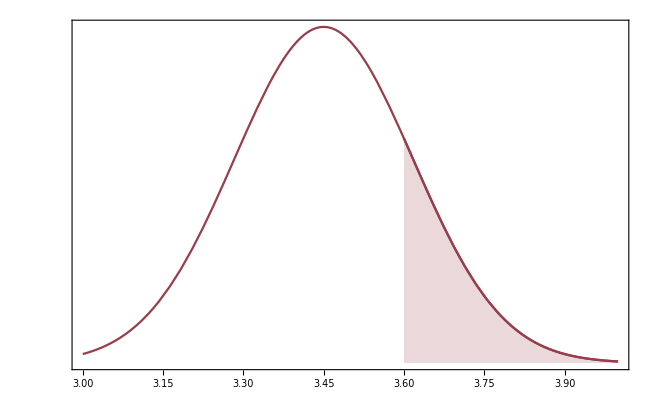
-Graphics- | 6 hours = 360 minutes

Pr(X_1+X_2+…+X_100>360min)=?
Pr(X̄>3.6min)=?

X̄~𝒩(mean=μ=3.45, SE=σ/(√n)=1.63/(√100)=0.163)

Z-score: 	Z=(3.6-3.45)/0.163=0.92

		Pr(Z>0.92)=0.179

## Log-Normal Distribution

A log-normal distribution is a distribution  where the  logarithm of the random variable x is normally distributed:

```mathematica
equation[𝒻[x,μ,σ]=="1/(x σ SqrtBox[2  π])""exp"parens[-(ln(x)-μ)^2/(2 σ^2)]]
```

𝒻(x,μ,σ)==1/(x σ SqrtBox[2  π]) exp (-(ln x-μ)^2/(2 σ^2))

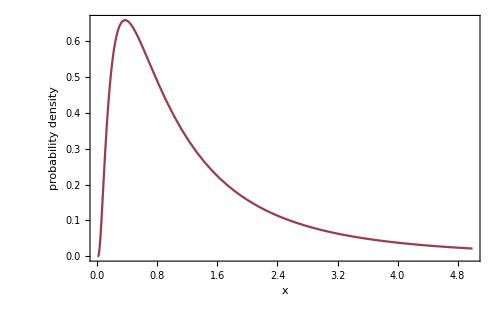

```mathematica
Plot[PDF[LogNormalDistribution[0,1],x],{x,0,5},Frame->True,Axes->False,BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,FrameLabel->{x,"probability density"}]
```

## Log-Normal Distribution

The PDF takes on its maximum value

```mathematica
equationNoBox[Subscript[𝒻, max]="1/(√(2  π))"exp parens[σ^2/2-μ]]
```

𝒻_max=1/(√(2  π)) exp (σ^2/2-μ)

at the position x_max=exp(μ-σ^2). The mean value (expectation value) and variance are:

```mathematica
equationNoBox["E(X)"="1/(σ SqrtBox[2  π])"∫_0^(+∞) x (exp parens[-("ln x"-μ)^2/(2 σ^2)])/x ⅆx=exp(μ+σ^2/2)]
equationNoBox["Var(X)"="1/(σ SqrtBox[2  π])"∫_0^(+∞) (x-("e")^(μ+σ^2/2))^2 (exp parens[-("ln x"-μ)^2/(2 σ^2)])/x ⅆx=exp(2μ+σ^2)parens[("e")^(σ^2)-1]]
```

E(X)=1/(σ SqrtBox[2  π]) ∫_0^(+∞) (x (exp (-(ln x-μ)^2/(2 σ^2))))/x ⅆx=exp (μ+σ^2/2)

Var(X)=1/(σ SqrtBox[2  π]) ∫_0^(+∞) ((x-e^(μ+σ^2/2))^2 (exp (-(ln x-μ)^2/(2 σ^2))))/x ⅆx=exp (2 μ+σ^2) (e^(σ^2)-1)

## Log-Normal Distribution

Given a random variable Y\[Distributed]𝒩(μ,σ), then the random variable X=e^Yis log-normally distributed. Given a particular target expectation value E and variance Var, it follows:

```mathematica
Row[{equationNoBox[σ^2="ln"(Var/("E")^2+1)],Spacer[20],"and",Spacer[20],equationNoBox[μ="ln(E)"-σ^2/2="ln"(("E")^2 √(1/(Var+("E")^2)))]}]
```

σ^2=ln (Var/E^2+1)andμ=ln(E)-σ^2/2=ln (E^2 √(1/(Var+E^2)))

## Log-Normal Distribution

### P.M.F. - probability mass function

```mathematica
equation[𝒻[x,μ,σ]=="1/(x σ SqrtBox[2  π])""exp"parens[-(ln(x)-μ)^2/(2 σ^2)]]
```

𝒻(x,μ,σ)==1/(x σ SqrtBox[2  π]) exp (-(ln x-μ)^2/(2 σ^2))

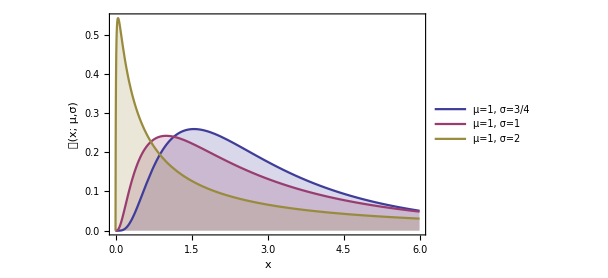
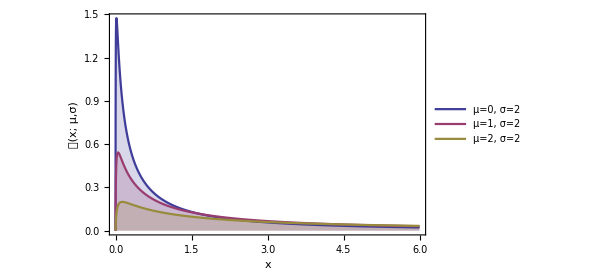
-Graphics- | -Graphics-

```mathematica
Grid[{{Plot[Evaluate@Table[PDF[LogNormalDistribution[1,σ],x],{σ,{.75,1,2}}],{x,0,6},Filling->Axis,PlotRange->All,Frame->True,FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450,PlotLegends->{"μ=1, σ=3/4","μ=1, σ=1","μ=1, σ=2"}],Plot[Evaluate@Table[PDF[LogNormalDistribution[μ,2],x],{μ,{0,1,2}}],{x,0,6},Filling->Axis,PlotRange->All,Frame->True,FrameLabel->{"x", "𝒫(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->450,PlotLegends->{"μ=0, σ=2","μ=1, σ=2","μ=2, σ=2"}]}},Spacings->2]
```

## Log-Normal Distribution

### CDF - cumulative distribution function

```mathematica
equation[ℱ[k";"μ,σ]==Pr parens[X≤k]==∫_(-∞)^k "1/(x σ SqrtBox[2  π])""exp"parens[-("ln" x-μ)^2/(2 σ^2)]ⅆx=1/2 parens[1+TraditionalForm@Erf[("ln" k-μ)/(√2 σ)]]=1/2 parens[TraditionalForm@Erfc[-("ln" k-μ)/(√2 σ)]]]
```

ℱ(k ; μ,σ)==Pr(X≤k)==∫_(-∞)^k 1/(x σ SqrtBox[2  π]) exp (-(ln x-μ)^2/(2 σ^2))ⅆx=1/2 (1+erf((ln k-μ)/(√2 σ)))=1/2 (erfc(-(ln k-μ)/(√2 σ)))

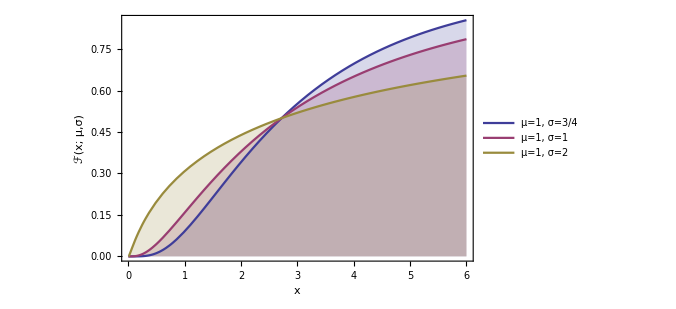
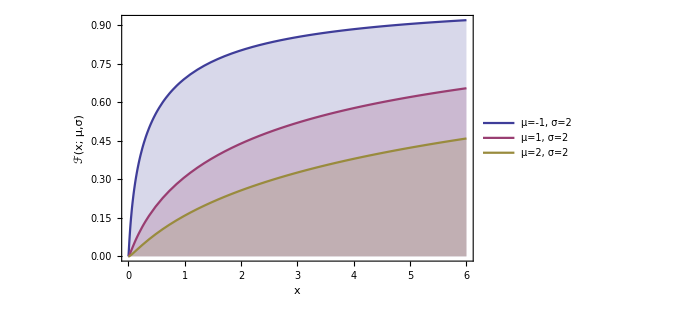
-Graphics- | -Graphics-

```mathematica
Grid[{{Plot[Evaluate@Table[CDF[LogNormalDistribution[1,σ],x],{σ,{.75,1,2}}],{x,0,6},Filling->Axis,PlotRange->All,Frame->True,FrameLabel->{"x", "ℱ(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,PlotLegends->Placed[{"μ=1, σ=3/4","μ=1, σ=1","μ=1, σ=2"},Below]],Plot[Evaluate@Table[CDF[LogNormalDistribution[μ,2],x],{μ,{-1,1,2}}],{x,0,6},Filling->Axis,PlotRange->All,Frame->True,FrameLabel->{"x", "ℱ(x; μ,σ)"},BaseStyle->{FontSize->16,Font->"Times"},ImageSize->500,PlotLegends->Placed[{"μ=-1, σ=2","μ=1, σ=2","μ=2, σ=2"},Below]]}},Spacings->2]
```

## Chebyshev’s Inequality

In probability theory, Chebyshev’s inequality guarantees that in any probability distribution, “nearly all” values are close to the mean — the precise statement being that no more than 1/k^2 of the distribution’s values can be more than k standard deviations away from the mean (or equivalently, at least 1 - 1/k^2 of the distribution’s values are within k standard deviations of the mean).

```mathematica
Row[{equation[𝒫[Abs[X-μ]≥k σ]≤1/k^2],Spacer[50],equation[𝒫[Abs[X-μ]≥k]≤σ^2/k^2],Spacer[50],equation[𝒫[Abs[X-μ]<k]≥1-σ^2/k^2]}]
```

𝒫(Abs[X-μ]≥k σ)≤1/k^2𝒫(Abs[X-μ]≥k)≤σ^2/k^2𝒫(Abs[X-μ]<k)≥1-σ^2/k^2

Only the case k > 1 provides useful information. When k < 1 the right-hand side is greater than one, so the inequality becomes vacuous, as the probability of any event cannot be greater than one. When k = 1 it just says the probability is less than or equal to one, which is always true for probabilities.

## Random numbers from probability distributions

Most number generators generate their output uniformly distributed (between 0  and 1). In general, we require numbers to be distributed according to a particular distribution. Let us define uniform deviates 𝓅(r) drawn from a standard probability density distributions that is uniform between r=0 and r=1.

```mathematica
equationInvBox[𝓅[r]=Piecewise[{{1,0≤r<1},{0,True}}]]
```

𝓅(r)=Piecewise[{{1, 0≤r<1}, {0, True}}]

The distribution is normalized so that

```mathematica
equationInvBox[∫_(-∞)^∞ 𝓅[r]ⅆr==∫_0^1 1ⅆr=1]
```

∫_(-∞)^∞ 𝓅(r)ⅆr==∫_0^1 1ⅆr=1

## Random numbers from probability distributions

We will refer to 𝓅(r) as the uniform distribution. Suppose that we require random deviates from a different normalized probability density distribution 𝒫(x) which is defined to be uniform between x=-1 and x=1; i.e. the distribution

```mathematica
equationInvBox[𝒫[x]==Piecewise[{{1/2,-1≤x<1},{0,True}}]]
```

𝒫(x)==(Piecewise[{{1/2, -1≤x<1}, {0, True}}])

## Random numbers from probability distributions

How to calculate x? If we choose a random deviate r between 0 and 1 from the uniform distribution, it is obvious that we can write

```mathematica
equationInvBox[x==𝒻[r]==2r-1]
```

x==𝒻(r)==2 r-1

which will be uniformly distributed between -1 and +1. This is an example of a simple linear transformation.

Let us generalize the approach. The task is to find a general relation for obtaining a random deviate x drawn from any probability density distribution 𝒫(x), in terms of the random deviate r drawn from the uniform probability distribution 𝓅(r).

Conservation of probability requires

```mathematica
equation[Abs[𝓅[r]ⅆr]==Abs[𝒫[x]ⅆx]]
```

Abs[𝓅(r) ⅆr]==Abs[𝒫(x) ⅆx]

## Random numbers from probability distributions

Therefore we can write

```mathematica
Row[{equationInvBox[∫_(-∞)^(" r") 𝓅[𝔯]ⅆ𝔯==∫_(-∞)^(" 𝔵") 𝒫[x]ⅆx],Spacer[10],Style["or",18],Spacer[10],equationInvBox[∫_0^(" r") 1ⅆ𝔯==∫_(-∞)^(" 𝔵") 𝒫[x]ⅆx]}]
```

∫_(-∞)^r 𝓅(𝔯)ⅆ𝔯==∫_(-∞)^𝔵 𝒫(x)ⅆxor∫_0^r 1ⅆ𝔯==∫_(-∞)^𝔵 𝒫(x)ⅆx

which gives the general result

```mathematica
equation[r==∫_(-∞)^(" 𝔵") 𝒫[x]ⅆx]
```

r==∫_(-∞)^𝔵 𝒫(x)ⅆx

Thus, to find 𝔵, selected randomly from the probability distribution 𝒫(x) , we generate a random number r from the uniform distribution and find the value of the limit 𝔵 that satisfies the general equation above.

## Random numbers from probability distributions

### Example

Consider the distribution

```mathematica
equationInvBox[𝓅[r]==Piecewise[{{A(1+a x^2),-1≤r<1},{0,True}}]]
```

𝓅(r)==(Piecewise[{{A (1+a x^2), -1≤r<1}, {0, True}}])

where 𝒫(x) is positive or zero everywhere within the specified range and the normalization constant A is chosen so that

```mathematica
equationInvBox[∫_-1^1 𝒫[x]ⅆx==1]
```

∫_-1^1 𝒫(x)ⅆx==1

## Random numbers from probability distributions

### Example

We have

```mathematica
equation[r==∫_(-∞)^(" 𝔵") 𝒫[x]ⅆx==∫_-1^(" 𝔵") A(1+a x^2)ⅆx==A(𝔵+(a 𝔵^3)/3+1+a/3)]
```

r==∫_(-∞)^𝔵 𝒫(x)ⅆx==∫_-1^𝔵 A (1+a x^2)ⅆx==A (𝔵+(a 𝔵^3)/3+1+a/3)

## Random numbers from probability distributions

### Example

And therefore to find 𝔵 we have to solve the third-degree equation

```mathematica
Solve[r==A(𝔵+(a 𝔵^3)/3+1+a/3),𝔵]//FullSimplify[#,Reals]&//TraditionalForm
```

{{𝔵→(2 2^(1/3) a A^2-2^(2/3) (√(a^3 A^4 ((a+1)^2 (a+4) A^2-6 a (a+3) A r+9 a r^2))+a^2 A^2 ((a+3) A-3 r))^(2/3))/(2 a A (√(a^3 A^4 ((a+1)^2 (a+4) A^2-6 a (a+3) A r+9 a r^2))+a^2 A^2 ((a+3) A-3 r))^(1/3))},{𝔵→-(-2^(1/3) A)/((√(a^3 A^4 ((a+1)^2 (a+4) A^2-6 a (a+3) A r+9 a r^2))+a^2 A^2 ((a+3) A-3 r))^(1/3))+((1-ⅈ √3) (√(a^3 A^4 ((a+1)^2 (a+4) A^2-6 a (a+3) A r+9 a r^2))+a^2 A^2 ((a+3) A-3 r))^(1/3))/(2 2^(1/3) a A)},{𝔵→(A Root-0.630+1.09 ⅈRoot[#1^3-2&,3]-0.6299605249474366)/((√(a^3 A^4 ((a+1)^2 (a+4) A^2-6 a (a+3) A r+9 a r^2))+a^2 A^2 ((a+3) A-3 r))^(1/3))+((1+ⅈ √3) (√(a^3 A^4 ((a+1)^2 (a+4) A^2-6 a (a+3) A r+9 a r^2))+a^2 A^2 ((a+3) A-3 r))^(1/3))/(2 2^(1/3) a A)}}

## Random numbers from probability distributions

### Example

This is called the transformation method of generating random deviates from probability distributions. In general, neither the integral equation, nor its solution can be obtained analytically, so numerical solutions are necessary. The following steps are required:

Decide on the range of x. Some probability density functions are defined in a finite range, others, such as the Gaussian extend to infinity. For numerical calculations, reasonable finite limits must be set.

Normalize the probability function. If it is necessary to impose limits on the range of the variable x, then the function must be renormalized to assure that the integral is unity over the newly defined range. The normalization integral should be calculated numerically by the same routine that is used to find x.

Generate a random variable r drawn from the uniform distribution.

Integrate the normalized probability function 𝒫(x) from negative infinity (or its defined lower limit) to the value x=𝔵, where 𝔵 satisfies the general result from above.

## Rejection Method

Often another method, the rejection method, is easier to use.

Suppose we wish to obtain random deviates between x=-1 and x=+1, drawn from the distribution function

```mathematica
equationInvBox[𝒫[x]==1+a x^2]
```

𝒫(x)==1+a x^2

We begin by generating a random deviate x' uniformly distributed between -1 and +1, corresponding to the allowed range of x, and a second random deviate y' uniformly distributed between 0 and (1+a), corresponding to the allowed range of 𝒫(x). We can see that x' and y' must be given by

```mathematica
equationInvBox[x'==-1+2 Subscript[r, i]"       and       "y'==(1+a)Subscript[r, i+1]]
```

x'==-1+2 r_i        and        y'==(1+a) r_(i+1)

where r_i and r_(i+1) are successively generated random numbers drawn from the uniform distribution.

## Rejection Method

We count an event as

a “hit” if the point {x',y'} falls between the curve defined by by 𝒫(x) and the x axis, that is, if y'<𝒫(x'), and

a “miss” if it falls above the curve.

In the limit of a large number of trials, the entire plot, including the area between the curve and the x axis will be uniformly populated by this operation and our selected samples will be the x coordinates of the “hits”, or the values of x' drawn randomly from the distribution 𝒫(x).

Note, that with this method it is not necessary to normalize the distribution to form a true probability function. It is sufficient that the distribution be positive and well behaved within its allowed range.

## Rejection Method

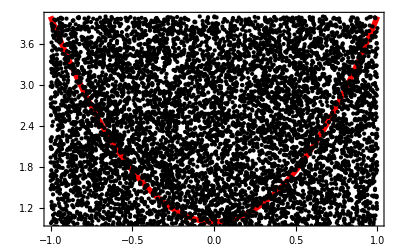
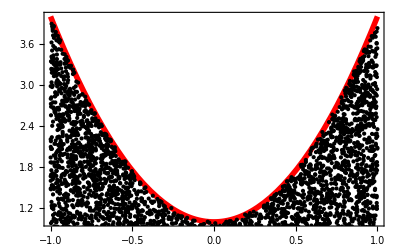
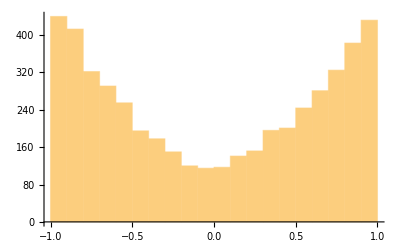
-Graphics- | -Graphics-
-Graphics- |

```mathematica
p[x_]:=Piecewise[{{1+3 x^2,-1≤x≤1},{0,True}}]
rand:={-1+2#[[1]],(1+3)#[[2]]}&@RandomReal[{0,1},2]
exp[n_]:=Table[rand,{n}]
With[{dat=exp[10000]},
Grid[{{Plot[p[x],{x,-1,1},Epilog->Point/@dat,ImageSize->400,PlotStyle->Directive[Red,Thickness[0.01]]],Plot[p[x],{x,-1,1},Epilog->Point/@(Select[dat,(#[[2]]<p[#[[1]]])&]),ImageSize->400,PlotStyle->Directive[Red,Thickness[0.01]]]},
{Histogram[Select[dat,(#[[2]]<p[#[[1]]])&][[All,1]],ImageSize->400],SpanFromLeft}}]]
Clear[p,rand,exp]
```

The advantage of this method is its simplicity. The disadvantage is its inefficiency. In a complex Monte Carlo program only a small fraction of the events may survive, especially for higher dimensional cases.

## Init

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SetOptions[$FrontEndSession,UnderoverscriptBoxOptions->{LimitsPositioning->False}]
```

```mathematica
ClearAll[equation]
Attributes[equation]={HoldAll,HoldAllComplete};
equation[eq___]:=TraditionalForm@Framed[HoldForm@Defer[eq],FrameStyle->Directive[Gray],FrameMargins->10]
ClearAll[equationNoBox]
Attributes[equationNoBox]={HoldAll,HoldAllComplete};
equationNoBox[eq___]:=TraditionalForm[HoldForm@Defer[eq]]
```

```mathematica
equation[ℱ[k,"N",ρ]==𝒫[X≤k]==∑_(n=0)^k Binomial["N",m] ρ^n(1-ρ)^("N"-n)]
```

ℱ(k,N,ρ)==𝒫(X≤k)==∑_(n=0)^k Binomial[N, m] ρ^n (1-ρ)^(N-n)

```mathematica
equationNoBox[ℱ[k,"N",ρ]==𝒫[X≤k]==∑_(n=0)^k Binomial["N",m] ρ^n(1-ρ)^("N"-n)]
```

ℱ(k,N,ρ)==𝒫(X≤k)==∑_(n=0)^k Binomial[N, m] ρ^n (1-ρ)^(N-n)

```mathematica
Attributes[equationInvBox]={HoldAll,HoldAllComplete};
equationInvBox[eq___]:=TraditionalForm@Framed[HoldForm@Defer[eq],FrameStyle->Transparent,FrameMargins->10]
```

```mathematica
Format[parens[e_]]:=Style[DisplayForm@RowBox[{"(",MakeBoxes@e,")"}],SpanMaxSize->Infinity]
Format[brackets[e_]]:=Style[DisplayForm@RowBox[{"[",MakeBoxes@e,"]"}],SpanMaxSize->Infinity]
Format[parens[e_,i_]]:=Style[DisplayForm@RowBox[{"(",MakeBoxes@e,")"}],SpanMaxSize->Infinity,SpanMinSize->i]
Format[brackets[e_,i_]]:=Style[DisplayForm@RowBox[{"[",MakeBoxes@e,"]"}],SpanMaxSize->Infinity,SpanMinSize->i]
 equationNoBox[Subscript[OverBar[parens[X/Y]],"geom"]==foo]
equation[Subscript[OverBar[brackets[X/Y]],"geom"]==foo]
equationNoBox[Subscript[OverBar[brackets[X/Y,3]],"geom"]==foo]
 equation[Subscript[OverBar[parens[X/Y]],"geom"]==foo]
equation[Subscript[OverBar[brackets[X/Y]],"geom"]==foo]
equation[Subscript[OverBar[parens[X/Y,BoxMargins->{{0,0},{0,0.5}}]],"geom"]==foo]
```

OverBar[(X/Y)]_geom==foo

OverBar[[X/Y]]_geom==foo

OverBar[[X/Y]]_geom==foo

OverBar[(X/Y)]_geom==foo

OverBar[[X/Y]]_geom==foo

OverBar[(X/Y)]_geom==foo

### Special cells

```mathematica
ToPictureCell[expr_]:=CellPrint[ExpressionCell[expr,"Picture",ShowStringCharacters->False]]
```

```mathematica
PicturePrint[expr_,opts:OptionsPattern[Cell]]:=CellPrint[TextCell[expr,"Picture",opts,ShowStringCharacters->False]]
```

### Set options

```mathematica
imgsize=500;
fontfam="Times";
fontsize=13;
sty =Directive[fontsize,FontFamily->fontfam];
```

```mathematica
SetOptions[#,BaseStyle->Thick,PlotStyle->ColorData[1,"ColorList"],ImageSize->imgsize,PlotRange->All,FillingStyle->Automatic,TicksStyle->Directive[fontsize,FontFamily->fontfam],Frame->True,Axes->False]&/@{Plot,ListPlot,LogPlot,LogLogPlot,ListLogLogPlot,LogLinearPlot,ListLogLinearPlot};
```

```mathematica
SetOptions[Histogram,{ImageSize->Large,BaseStyle->{Directive[fontsize,FontFamily->fontfam]}}];
```

```mathematica
SetOptions[{Histogram3D,DensityHistogram},{ImageSize->Medium,BaseStyle->{Directive[fontsize,FontFamily->fontfam]}}];
```

```mathematica
OverviewMouseover[header_,subs_]:=CellPrint@Cell[BoxData[ToBoxes@Mouseover[Framed[Style[header,"OverviewSection"],FrameMargins->{{15,15},{5,5}},BoxFrame->2,FrameStyle->None,RoundingRadius->5],

Evaluate@If[subs=="",Framed[Style[header,"OverviewSection",White],FrameMargins->{{15,15},{5,5}},BoxFrame->2,FrameStyle->None,RoundingRadius->5,Background->m8red[1]],Row[{Framed[Style[header,"OverviewSection",White],FrameMargins->{{15,15},{5,5}},FrameStyle->None,RoundingRadius->5,Background->m8red[1]]," » ",Framed[Style[subs,"OverviewSection"],FrameMargins->{{15,15},{5,5}},FrameStyle->m8red[1],BoxFrame->2,RoundingRadius->5,Background->White]}]]]],"OverviewSection"]
```

```mathematica
LargeOverviewMouseover[header_,subs_]:=CellPrint@Cell[BoxData[ToBoxes@Mouseover[Framed[Style[header,"LargeOverviewSection"],FrameMargins->{{15,15},{5,5}},BoxFrame->2,FrameStyle->None,RoundingRadius->5],

Evaluate@If[subs=="",Framed[Style[header,"LargeOverviewSection",White],FrameMargins->{{15,15},{5,5}},BoxFrame->2,FrameStyle->None,RoundingRadius->5,Background->m8red[1]],Row[{Framed[Style[header,"LargeOverviewSection",White],FrameMargins->{{15,15},{5,5}},FrameStyle->None,RoundingRadius->5,Background->m8red[1]]," » ",Framed[Style[subs,"LargeOverviewSection"],FrameMargins->{{15,15},{5,5}},FrameStyle->m8red[1],BoxFrame->2,RoundingRadius->5,Background->White]}]]]],"LargeOverviewSection"]
```

```mathematica
MapThread[LargeOverviewMouseover,Transpose[{{"What is Mathematica?","Uses, community, prebuilt materials"},{"A Look at Workflow","syntax, palettes, free-form input"},{"Mathematica in the Classroom","teaching and learning applications"},{"Work with Data","built-in curated data, your own data"}}]];
```

```mathematica
Clear[numberLine];
numberLine[ssize_]:={SeedRandom[1234];
Block[{data=RandomReal[{-1,1},20],mean,dev,sample,pos,smean,sdev},
mean=Mean[data];
dev=1/Length[data] Total[(data-mean)^2];
SeedRandom[];
sample=RandomChoice[data,ssize];
pos=Position[data,#]&/@sample;
smean=Mean[sample];sdev=1/Length[sample] Total[(sample-smean)^2];
Sow[{smean,sdev}];
Graphics[{
PointSize[Large],Red,Point[{#,0.05}]&/@data,
Black,Thick,Arrowheads[{-.03,.03}],Arrow[{{-1,0},{1,0}}],
Line[{{mean,0.05},{mean,-0.05}}],
Line[{{mean+dev,0.0},{mean+dev,-0.05}}],Line[{{mean-dev,0.0},{mean-dev,-0.05}}],
Circle[{#,0.05},0.03]&/@sample,
Orange,
Line[{{smean,0.05},{smean,-0.05}}],
Line[{{smean+sdev,0.0},{smean+sdev,-0.05}}],Line[{{smean-sdev,0.0},{smean-sdev,-0.05}}],},ImageSize->700,
PlotLabel->Row[{"μ=",mean,"  σ^2=",dev}]]]}
```